# Baseball, the Mathematica Package.

## Exploring Baseball with Retrosheet and Mathematica

Version 2.6

Ken Levasseur
klevasseur@mac.com

The data files used here were obtained free of charge from and is copyrighted by Retrosheet.  Interested parties may contact Retrosheet at "www.retrosheet.org".

-Graphics- This work is licensed under a Creative Commons Attribution-NonCommercial-ShareAlike 3.0 United States License.

Note:  As of November 2012, event files of all major league games from 1974 to 2012 are available  Prior event file years (1945-1973) are not complete.
2017 update:

## Introduction

Load the package before doing anything else.

```mathematica
<<Baseball`
```

/Users/ken_l/Library/Mathematica/Applications/Baseball/

## retrogames

When one or more games are loaded from Retrosheet event files, the package will automatically format each game into a Mathematica expression with head retrogame.   The arguments of a retrogame are the lines in the event file for the corresponding game.  The expression itself doen't appear in the output, but all the information is present.

```mathematica
aGame=First[AllEvents["CHA",2005]]
```

CLE @ CHA on 2005/04/04

```mathematica
Head[aGame]
```

retrogame

Several functions will extract specific information from a retrogame.

```mathematica
Temperature[aGame]
```

64

```mathematica
StartingPitchers[aGame]
```

(westj001 | Jake Westbrook
buehm001 | Mark Buehrle)

You can also use Mathematica functions to build your own functions.  Here, the function StolenBases is defined to list the stolen based in a retrogame.

Note:  this function isn't defined within the package as of the current version.

```mathematica
StolenBases[g_retrogame]:=Module[{sbl,v,h},v=VisitingTeam[g];h=HomeTeam[g];sbl=List@@Select[g,Result[#]=="SB"&];If[sbl=={},{},(List@@#&/@sbl)//Transpose//{#[[2]]/.{0->v,1->h},#[[3]],#[[6]]}&//Transpose]]
```

Here we extract information on the stolen bases in a single game.  The only stolen base was by A.J. Pierzynski, whose retrosheet player code is "piera001."  More on player codes later.

```mathematica
StolenBases[aGame]
```

(CHA | piera001 | SB2)

A stolen base in game 1 of the season is a good start.  How many did  Pierzynski steal in 2005?

```mathematica
Select[Join@@(StolenBases/@AllEvents["CHA",2005]),#[[2]]=="piera001"&]
```

(CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2
CHA | piera001 | SB2)

Actually, you need to be careful.  We're only looking at the White Sox games right now. And we can tell A. J.  didn't seal any bases against  the White Sox.  We can verify that he only played for one team using the TeamsPlayedFor function.

```mathematica
TeamsPlayedFor["piera001",{2005,2005}]
```

{{piera001,A.J. Pierzynski},(2005 | {CHA})}

## Game Logs

Some information is most easily retrieved from the game log corresponding to a game.  Here is what game log information looks like.

```mathematica
GameLogData[aGame]
```

{20050404,0,Mon,CLE,AL,1,CHA,AL,1,0,1,51,D,,,,CHI12,38141,111,0,00000010x,27,2,0,0,0,0,0,0,0,1,0,6,0,0,2,0,1,1,1,1,0,0,24,16,1,0,1,0,28,4,1,0,0,1,0,0,0,1,0,3,1,0,1,0,4,2,0,0,0,0,27,13,0,0,2,0,reedr901,Rick Reed,craft901,Terry Craft,barrt901,Ted Barrett,marqa901,Alfonso Marquez,,(none),,(none),wedge001,Eric Wedge,guilo001,Ozzie Guillen,buehm001,Mark Buehrle,westj001,Jake Westbrook,takas001,Shingo Takatsu,rowaa001,Aaron Rowand,westj001,Jake Westbrook,buehm001,Mark Buehrle,crisc001,Coco Crisp,8,bellr002,Ron Belliard,4,hafnt001,Travis Hafner,10,martv001,Victor Martinez,2,boona001,Aaron Boone,5,blakc001,Casey Blake,9,broub001,Ben Broussard,3,hernj001,Jose Hernandez,7,peraj001,Jhonny Peralta,6,podss001,Scott Podsednik,7,iguct001,Tadahito Iguchi,4,everc001,Carl Everett,10,konep001,Paul Konerko,3,dye-j001,Jermaine Dye,9,rowaa001,Aaron Rowand,8,piera001,A.J. Pierzynski,2,credj001,Joe Crede,5,uribj002,Juan Uribe,6,,Y}

Some functions will extract information directly from this data.

```mathematica
BasicScoreboard[aGame]
```

({2005,4,4} | Comiskey Park II | Chicago | IL
CLE | 0 | 2 | 1
CHA | 1 | 4 | 0)

There is much more more information in game logs, some of which we will review later.

Starting with a game log item, you can retrieve the retrogame, which has even more detail.

```mathematica
Retrogame[First[GameLogs[1984]]]
```

CHA @ BAL on 1984/04/02

### SeasonPlot

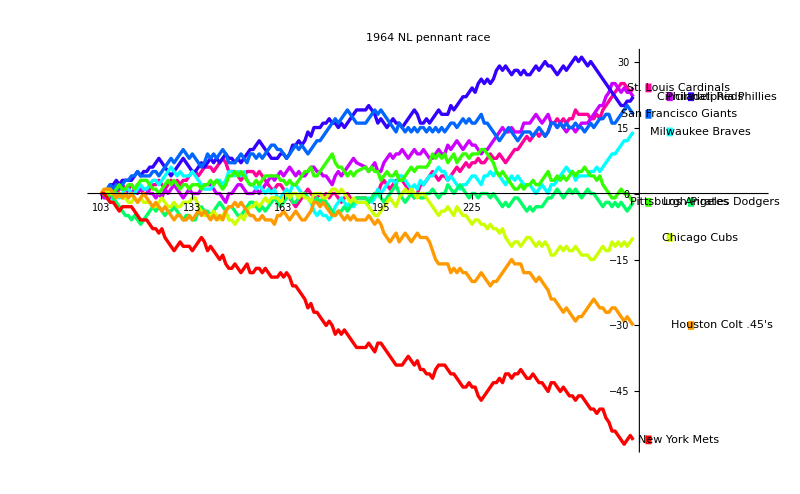

```mathematica
SeasonPlot[1964,"NL"]
```

## Player Codes

Earlier, we ran across a player code "piera001" and knowing that it was from a White Sox player in 2005, we got the player's name using FromPlayerCode:

```mathematica
FromPlayerCode["piera001","CHA",2005]
```

A.J. Pierzynski

However, you can convert from playercode to player name without any other information provided.

```mathematica
FromPlayerCode["piera001"]
```

A.J. Pierzynski

The output of FromPlayerCode is actually more complicated than it appears.  It is really an expression that includes the playercode, first and last names of the players, but the output format is just to display the name as a single string.  Here is a view of the FullForm of the output.

```mathematica
FullForm[FromPlayerCode["piera001"]]
```

PlayerName[List["piera001","Pierzynski","A.J."]]

Retrosheet player codes contain the first four (lower-case) letters of the player's last name, the first letter of the first name, followed by three digits.   The first modern player with any specific letter combination has the digits 001 appended as a suffix.   Older players start with 101.

A modern player is a player defined as any player who played at least one game in 1984 or later.  When I first read this definition though Minnie Minoso was going to be "modern" but it turns out that his career was from 1949 to 1980.  I guess I was thinking of the following incidents, taken from Minnie's SABR biography:

In 1993, at the age of 70, Minnie signed a contract with the independent St. Paul Saints. He grounded out in his only at-bat for the team. The ball and bat were sent to Cooperstown to mark the moment when pro baseball had its first six-decade player. In 2003, Minnie was at it again, pinch-hitting for the Saints. He took three pitches for balls, then let a fourth pitch go by and trotted toward the first base bag, still hoping to "steal first." The umpire would have none of it, calling a strike, Minnie fouled off the next pitch before letting ball four pass and walking into the history books as a seven-decade pro. His contract, prorated for one game, paid him 32 bucks.

```mathematica
FromPlayerCode["minom101"]
```

Minnie Minoso

```mathematica
FromPlayerCode["ellsj001"]
```

Jacoby Ellsbury

Josh Beckett has a player code starting with  "beckj"  but Joe Beckwith took the 001 suffix. That's a classic "hash clash" and its simply handled by given Beckett the suffix 002.

```mathematica
FromPlayerCode["beckj001"]
```

Joe Beckwith

```mathematica
FromPlayerCode["beckj002"]
```

Josh Beckett

```mathematica
FromPlayerCode["wangc001"]
```

Chien-Ming Wang

If baseball becomes popular in China, look for this code to get mutlple suffixes since there are millions of Wangs in China.

Umpires also have "playercodes"  using the same system - umpire suffixes start with 901.  Here is the home plate umpire in the White Sox' first game of 2005

```mathematica
HomePlateUmpire[aGame]
```

{reedr901,Rick Reed}

The output identifies Rick Reed as being "reedr901" but if you encounter just the code,

```mathematica
FromPlayerCode["reedr901"]
```

Rick Reed

## Contents of a retrogame

Each retrogame is a sequence of expressions with a variety of Heads.

id | Single argument identifying the game
version | obsolete
info | miscellaneous information about the game
start | contains information on starting players
sub | contains informaiton on substitutes
play | contains information on plays in the game
badj | adjust batting side when not standard
e. g. batting left against a LHP.
padj | pitcher's version of badj.  
ladj | used when teams bat out of order
data | such as earned runs allowed by a pitcher in the game
com | comments

For details on the scope of these items see http://www.retrosheet.org/eventfile.htm

```mathematica
g=AllEvents["MON",1995][[-4]]
```

CIN @ MON on 1995/09/28

Every game has a unique ID indicating the home team, the date on which the game was played, and whether it was a single game (0), or part of a doubleheader (1/2).

```mathematica
ID[g]
```

MON199509280

Many types of information are contained in info expressions.   In future versions, much of this data may be accessed through functions.

```mathematica
Select[g,#[[1]]=="attendance"&]//First
```

info(attendance,14581)

Here is how to find out who was first base umpire.

```mathematica
Select[g,#[[1]]=="ump1b"&]//First//Append[#,FromPlayerCode[#[[2]]]]&
```

info(ump1b,wintm901,Mike Winters)

You can scan the next output to get a sense of what else is included.

```mathematica
List@@g//TableForm
```

id(MON199509280)
version(1)
info(visteam,CIN)
info(hometeam,MON)
info(site,MON02)
info(date,1995/09/28)
info(number,0)
info(starttime,7:41)
info(daynight,night)
info(usedh,false)
info(umphome,davig901)
info(ump1b,wintm901)
info(ump2b,tatat901)
info(ump3b,grege901)
info(pitches,pitches)
info(temp,68)
info(winddir,unknown)
info(windspeed,0)
info(fieldcond,dry)
info(precip,none)
info(sky,dome)
info(timeofgame,181)
info(attendance,14581)
info(wp,schop001)
info(lp,martp001)
info(save,branj001)
start(howat001,Thomas Howard,0,1,8)
start(larkb001,Barry Larkin,0,2,6)
start(gantr001,Ron Gant,0,3,7)
start(sandr002,Reggie Sanders,0,4,9)
start(morrh001,Hal Morris,0,5,3)
start(santb001,Benito Santiago,0,6,2)
start(boonb002,Bret Boone,0,7,4)
start(branj002,Jeff Branson,0,8,5)
start(schop001,Pete Schourek,0,9,1)
start(whitr001,Rondell White,1,1,8)
start(segud001,David Segui,1,2,3)
start(beniy001,Yamil Benitez,1,3,9)
start(berrs001,Sean Berry,1,4,5)
start(cordw001,Wil Cordero,1,5,7)
start(lansm001,Mike Lansing,1,6,4)
start(grudm001,Mark Grudzielanek,1,7,6)
start(laket001,Tim Laker,1,8,2)
start(martp001,Pedro J. Martinez,1,9,1)
play(1,0,howat001,10,BX,43/G4)
play(1,0,larkb001,11,BFX,9/F9S)
play(1,0,gantr001,22,BBCSS,K)
play(1,1,whitr001,0,X,S7/G56)
play(1,1,segud001,32,C1F1BF11BFBX,5/P15/DP.1X1(53))
play(1,1,beniy001,1,CX,D7/L7L)
play(1,1,berrs001,0,S,PB.2-3)
play(1,1,berrs001,1,S.X,63/G6S)
play(2,0,sandr002,10,BX,8/F8LXD)
play(2,0,morrh001,21,BBFX,6/L6D)
play(2,0,santb001,0,H,HP)
play(2,0,boonb002,32,BFB1CBX,E8/F8RD.1-H(NR)(UR);B-2)
play(2,0,branj002,12,CFBS,K)
play(2,1,cordw001,22,BBFCS,K)
play(2,1,lansm001,11,FBX,6/P56D)
play(2,1,grudm001,12,SFBFC,K)
play(3,0,schop001,0,X,31/G34)
play(3,0,howat001,12,FBFT,K)
play(3,0,larkb001,1,CX,9/F9D)
play(3,1,laket001,0,.,NP)
sub(taube001,Ed Taubensee,0,6,2)
play(3,1,laket001,32,..BBBCFC,K)
play(3,1,martp001,0,H,HP)
play(3,1,whitr001,22,BSSBX,D9/L3D.1-3)
play(3,1,segud001,0,X,D7/G5L.3-H;2-H)
play(3,1,beniy001,2,SFS,K)
play(3,1,berrs001,32,FFFBFFBFBX,9/F9M)
play(4,0,gantr001,30,.BBBB,W)
play(4,0,sandr002,21,FB1BB,SB2)
play(4,0,sandr002,32,FB1BB.FS,K)
play(4,0,morrh001,1,FX,9/F9M)
play(4,0,taube001,22,SBSBFX,S7/F89M.2-H)
play(4,0,boonb002,12,CBCFX,S7/L7M.1-2)
play(4,0,branj002,32,CBBBFFFX,D9/L89M.2-H;1-H)
play(4,0,schop001,11,BSX,43/G4D)
play(4,1,cordw001,10,BH,HP)
play(4,1,lansm001,12,SFBX,684(1)/FO/P6MD)
play(4,1,grudm001,21,BC1B11,POCS2(136))
play(4,1,grudm001,21,BC1B11.X,4/P4D)
play(5,0,howat001,11,BSX,8/L8LM)
play(5,0,larkb001,21,BCBX,53/G5)
play(5,0,gantr001,22,BBCFX,4/P4MD)
play(5,1,laket001,10,BX,D8/L8RM)
play(5,1,martp001,0,.,NP)
sub(siddj001,John Siddall,1,8,12)
play(5,1,martp001,10,..BX,34/BG13S)
play(5,1,whitr001,2,FFFX,D6/G6M.2-H)
play(5,1,segud001,11,FBX,3/G3.2-3)
play(5,1,beniy001,32,BCBFFBC,K)
play(6,0,sandr002,0,,NP)
sub(siddj001,John Siddall,1,8,2)
play(6,0,sandr002,22,.FBCBS,K)
play(6,0,morrh001,10,BX,S9/G34)
play(6,0,taube001,30,BBBB,W.1-2)
play(6,0,boonb002,2,CSS,K)
play(6,0,branj002,32,FBBFBB,W.2-3;1-2)
play(6,0,schop001,2,CSS,K)
play(6,1,berrs001,12,FFBX,6/P6MD)
play(6,1,cordw001,2,SSS,K)
play(6,1,lansm001,12,SCBX,S7/G56)
play(6,1,grudm001,0,X,4/P34D)
play(7,0,howat001,1,CX,D7/F7LD)
play(7,0,larkb001,22,FBFFBX,S8/G6MD.2-H;B-3(E3/TH))
play(7,0,gantr001,0,,NP)
sub(hereg001,Gil Heredia,1,9,1)
play(7,0,gantr001,21,.BBCX,8/SF/F8LXD.3-H)
play(7,0,sandr002,2,CSC,K)
play(7,0,morrh001,0,X,S9/G34)
play(7,0,taube001,10,BX,7/F78M)
play(7,1,siddj001,0,,NP)
sub(jackm001,Mike Jackson,0,3,1)
play(7,1,siddj001,0,.,NP)
sub(waltj001,Jerome Walton,0,1,7)
play(7,1,siddj001,0,..,NP)
sub(lewid001,Darren Lewis,0,2,8)
play(7,1,siddj001,0,...,NP)
sub(duncm001,Mariano Duncan,0,9,6)
play(7,1,siddj001,31,....BBCBX,7/F78S)
play(7,1,hereg001,0,,NP)
sub(floyc001,Cliff Floyd,1,9,11)
play(7,1,floyc001,22,.CFBFBS,K)
play(7,1,whitr001,2,SSS,K)
play(8,0,boonb002,0,,NP)
sub(floyc001,Cliff Floyd,1,9,8)
play(8,0,boonb002,0,.,NP)
sub(frasw001,Willie Fraser,1,1,1)
play(8,0,boonb002,10,..BX,63/G6)
play(8,0,branj002,31,CBBBB,W)
play(8,0,duncm001,2,SFX,E4/G4.1-2)
play(8,0,waltj001,10,BX,HR/F7D.2-H;1-H(UR);B-H)
play(8,0,lewid001,22,BCBCX,43/G4M)
play(8,0,jackm001,0,,NP)
sub(harrl001,Lenny Harris,0,3,11)
play(8,0,harrl001,22,.CBFBX,6/P6M)
play(8,1,segud001,0,,NP)
sub(pught001,Tim Pugh,0,3,1)
play(8,1,segud001,32,.BCFBBX,7/L7M)
play(8,1,beniy001,12,SCBX,5/P5D)
play(8,1,berrs001,22,BCBSS,K)
play(9,0,sandr002,0,,NP)
sub(harrg001,Greg A. Harris,1,1,1)
play(9,0,sandr002,0,.X,63/G6)
padj(harrg001,L)
play(9,0,morrh001,30,.BBBB,W)
padj(harrg001,L)
play(9,0,taube001,32,CBBBCFX,23/G13S.1-2)
play(9,0,boonb002,22,.BFCBX,13/G23)
play(9,1,cordw001,10,BX,4/P4D)
play(9,1,lansm001,21,BBSX,2/P25F)
play(9,1,grudm001,11,FBX,D9/F89XD)
play(9,1,siddj001,32,FBFBFBB,W)
play(9,1,floyc001,0,,NP)
sub(mcelc001,Chuck McElroy,0,3,1)
play(9,1,floyc001,0,.,NP)
sub(silvd001,Dave Silvestri,1,9,11)
play(9,1,silvd001,11,..CBX,S9/L9M.2-3;1-2)
play(9,1,harrg001,0,,NP)
sub(andrs001,Shane Andrews,1,1,11)
play(9,1,andrs001,0,.X,HR/F9D.3-H;2-H;1-H)
play(9,1,segud001,0,,NP)
sub(branj001,Jeff Brantley,0,3,1)
play(9,1,segud001,31,.CBBBB,W)
play(9,1,beniy001,32,BBCSBX,53/G56)
data(er,schop001,3)
data(er,jackm001,0)
data(er,pught001,2)
data(er,mcelc001,2)
data(er,branj001,0)
data(er,martp001,5)
data(er,hereg001,0)
data(er,frasw001,2)
data(er,harrg001,0)

## Play Results

Individual plays within a game are described win play expressions. Here is the first play of the first game of the White Sox 2005 season.   Coco Crisp of the Indians  grounded out, second to first.

```mathematica
aGame//Select[#,Head[#]==play&]&//First
```

play(1,0,crisc001,11,BFX,43/G)

A variety of functions will extract these plays.  We describe them with examples.  Here are all of Crisp's at-bats (really plate appearances)  in the same game.

```mathematica
PlayerAtBats["crisc001",aGame]
```

(CHA200504040 | play(1,0,crisc001,11,BFX,43/G)
CHA200504040 | play(4,0,crisc001,22,BCFFFBFC,K)
CHA200504040 | play(7,0,crisc001,1,MX,S8/L)
CHA200504040 | play(9,0,crisc001,22,CBBFX,31/G))

It takes a bit more time, but you can get the pitcher code with each at-bat.

```mathematica
PlayerAtBats["crisc001",aGame,WithPitchers->True]
```

(CHA200504040 | play(1,0,crisc001,11,BFX,43/G) | buehm001
CHA200504040 | play(4,0,crisc001,22,BCFFFBFC,K) | buehm001
CHA200504040 | play(7,0,crisc001,1,MX,S8/L) | buehm001
CHA200504040 | play(9,0,crisc001,22,CBBFX,31/G) | takas001)

All plate appearances for the 2005 season is generated but not displayed here.

```mathematica
Coco2005=PlayerAtBats["crisc001",2005];
```

The number of play records will generally be greater than the actual plate appearances.  When a balk or wild pitch occurs during an at-bat, the actual at-bat is split between two or more play expression.

```mathematica
Length[Coco2005]
```

686

Here at Crisp's home runs in 2005.

```mathematica
HomeRuns["crisc001",2005]
```

(CHA200504070 | play(9,0,crisc001,22,BCCBX,HR/9/F)
ANA200505090 | play(3,0,crisc001,20,BBX,HR/89/F)
ANA200505100 | play(9,0,crisc001,21,.CBBX,HR/9/F)
MIN200506020 | play(4,0,crisc001,0,X,HR/78/F)
CHA200506030 | play(3,0,crisc001,11,*BFX,HR/9L/F.3-H;2-H)
CHA200506050 | play(4,0,crisc001,10,BX,HR/7/F.1-H)
SDN200506090 | play(8,0,crisc001,10,BX,HR/9/F)
DET200508050 | play(6,0,crisc001,10,BX,HR/7/F.3-H)
TBA200508220 | play(1,0,crisc001,31,BBBCX,HR/9/F)
DET200509060 | play(3,0,crisc001,20,1BBX,HR/9/F.1-H)
CLE200509080 | play(6,1,crisc001,22,FFFFBBX,HR/7/F)
CLE200509100 | play(3,1,crisc001,21,BCBX,HR/9/F)
CLE200509170 | play(1,1,crisc001,31,B>B.F*BX,HR/8/F.2-H)
KCA200509220 | play(7,0,crisc001,32,BCBBFX,HR/78/F.1-H)
KCA200509240 | play(8,0,crisc001,21,F*BBX,HR/9/F.1-H))

This takes a long time!  Hank Aaron hit 755 home runs in his career.  Not quite all of them are recorded in the event files.   As of 2017, 737 are found.

```mathematica
AaronHrs=HomeRuns["aaroh101",#]&/@(Range@@FirstYearLastYear["aaroh101"]);
```

```mathematica
Map[Length,AaronHrs]//{Transpose[{Range@@FirstYearLastYear["aaroh101"],#}],Plus@@#}&
```

{(1954 | 12
1955 | 23
1956 | 22
1957 | 44
1958 | 30
1959 | 39
1960 | 40
1961 | 34
1962 | 45
1963 | 42
1964 | 24
1965 | 32
1966 | 42
1967 | 38
1968 | 29
1969 | 44
1970 | 38
1971 | 46
1972 | 33
1973 | 38
1974 | 20
1975 | 12
1976 | 10),737}

Let's examine Carl Yastramski's extra-base hits in 1967

```mathematica
YazExtra07=Select[PlayerAtBats["yastc101",#]&/@AllEvents["BOS",1967]//Flatten,ResultQ[{"Double","Triple","HomeRun"},#]&]
```

{play(1,0,yastc101,??,,T7.1-H),play(3,0,yastc101,??,,T7),play(17,0,yastc101,??,,D7),play(5,1,yastc101,??,,D7.1-H),play(1,1,yastc101,??,,HR/7),play(1,1,yastc101,??,,HR/7.2-H),play(4,0,yastc101,??,,D7.3-H;1-H),play(7,0,yastc101,??,,D7.1-3),play(9,0,yastc101,??,,D.3-H;2-H;1-H),play(1,0,yastc101,??,,D.2-H;1-3),play(5,0,yastc101,??,,D),play(1,1,yastc101,??,,HR/8),play(2,1,yastc101,??,,HR/7),play(7,1,yastc101,??,,HR/9),play(5,1,yastc101,??,,HR.2-H),play(7,1,yastc101,??,,HR.2-H),play(1,1,yastc101,??,,D),play(8,1,yastc101,??,,T.3-H;1-H),play(8,0,yastc101,??,,HR/9.3-H),play(4,1,yastc101,??,,HR/8),play(6,1,yastc101,??,,HR/9),play(6,0,yastc101,??,,HR.1-H),play(1,0,yastc101,??,,D9),play(4,0,yastc101,??,,D8),play(1,0,yastc101,??,,D9.2-H),play(6,0,yastc101,??,,HR/8),play(5,1,yastc101,??,,HR/9.1-H(UR)),play(7,1,yastc101,??,,HR/9),play(1,1,yastc101,??,,D9),play(5,1,yastc101,??,,D7.1-H),play(7,1,yastc101,??,,HR),play(3,0,yastc101,??,,D8.3-H;2-H),play(9,0,yastc101,??,,HR/9.1-H),play(5,0,yastc101,??,,HR/9),play(7,1,yastc101,??,,D9.1-3),play(3,1,yastc101,??,,HR/9.1-H),play(4,0,yastc101,??,,D9),play(8,0,yastc101,??,,HR/7),play(4,1,yastc101,??,,D9.1-3),play(6,1,yastc101,??,,HR/9),play(7,1,yastc101,??,,HR/9),play(1,1,yastc101,??,,D9.2-H),play(8,1,yastc101,??,,HR/7.1-H),play(8,0,yastc101,??,,HR/7),play(5,0,yastc101,??,,HR/9),play(7,1,yastc101,??,,D8.3-H(UR);2-H(UR);1-H(UR);BXH(23)(E8)#),play(1,1,yastc101,??,,HR/8),play(3,1,yastc101,??,,HR/9.2-H;1-H),play(6,1,yastc101,??,,HR/8.3-H;1-H),play(1,1,yastc101,??,,D7.1-3),play(3,1,yastc101,??,,D9),play(9,0,yastc101,??,,D7),play(3,0,yastc101,??,,D7.1-3),play(8,1,yastc101,??,,HR/8),play(6,1,yastc101,??,,HR/7.1-H),play(8,1,yastc101,??,,D9),play(6,1,yastc101,??,,HR/9.3-H;1-H),play(5,1,yastc101,??,,HR/7.2-H;1-H),play(3,1,yastc101,??,,D8),play(4,1,yastc101,??,,HR/9),play(5,0,yastc101,??,,T8),play(5,0,yastc101,??,,HR/9),play(7,0,yastc101,??,,HR/9),play(11,0,yastc101,??,,HR/9),play(6,0,yastc101,??,,HR/8.1-H(UR)),play(4,0,yastc101,??,,HR/7.2-H(UR);1-H(UR);B-H(UR)),play(7,0,yastc101,??,,HR/7),play(5,1,yastc101,??,,HR/8),play(6,1,yastc101,??,,D7),play(3,1,yastc101,??,,D9.3-H;2-H),play(1,0,yastc101,??,,D8.2-H),play(9,0,yastc101,??,,HR/9),play(6,0,yastc101,??,,HR/7),play(7,0,yastc101,??,,D9),play(5,0,yastc101,??,,HR/7.1-H),play(5,1,yastc101,??,,D9),play(7,1,yastc101,??,,HR/8.2-H;1-H),play(7,1,yastc101,??,,HR/9.2-H;1-H(UR)),play(4,1,yastc101,??,,D7)}

```mathematica
Length[YazExtra07]
```

79

We can partition the extra-base hits by type and then take the lengths.  The totals can be verified at http://www.retrosheet.org/boxesetc/Y/Pyastc101.htm.

```mathematica
Length/@Map[Select[YazExtra07,#]&,{DoubleQ,TripleQ,HomeRunQ}]
```

{31,4,44}

## Pitchs and Counts

Recent retrosheet data included individual pitch data for each at-bat.  Lets look at the pitches in a single half inning of a game.   Here is the ninth inning of Clay Buchholz' no hitter on September 1, 2007.

```mathematica
anInning=InningsWithPitchers[AllEvents["BOS",2007][[136]]]//Last
```

(BOS200709010 | play(9,0,robeb003,12,CBSFS,K) | buchc001
BOS200709010 | play(9,0,pattc001,21,BBCX,8/L) | buchc001
BOS200709010 | play(9,0,markn001,12,BCFC,K) | buchc001)

The following function has not been added to the package as of V2.7.

```mathematica
RunningCount[p_play]:=Module[{c},c=p[[5]]//Characters//(#/.{{s___,"X"}->{s}})&//Map[If[#==="B",{1,0},{0,1}]&,#]&//FoldList[{#1[[1]]+#2[[1]],Min[2,#1[[2]]+#2[[2]]]}&,{0,0},#]&//Rest;If[p[[6]]=="K",c[[Length[c],2]]=c[[Length[c],2]]+1];If[(p[[6]]=="W")||(p[[6]]=="IW"),c[[Length[c],1]]=c[[Length[c],1]]+1];c]
```

Here is a running count for the first batter.

```mathematica
RunningCount[anInning[[1,2]]]
```

(0 | 1
1 | 1
1 | 2
1 | 2
1 | 3)

This function has also not  been added.

```mathematica
PitchesThrown[p_play]:=p[[5]]//StringLength
```

```mathematica
PitchesThrown[anInning[[1,2]]]
```

5

PitchCallTotals has been added and produces some interesting observations on umpires. Let's look at the pitch calls form the Red Sox' first game of 2007.

```mathematica
PitchCallTotals[First[AllEvents["BOS",2007]]]
```

{56,102,123}

Tim Tschida called 56 strikes, 102 balls and 123 pitches needed no call (including intentional balls)

```mathematica
HomePlateUmpire[First[AllEvents["BOS",2007]]]
```

{tscht901,Tim Tschida}

Lets compute something more ambitious.  First lets identify all home plate umpire codes in 2007.

```mathematica
umps=Map[(HomePlateUmpire[#]//First)&,GameLogs[2007]]//Union
```

{barkl901,barrs901,barrt901,bellw901,buckc901,campa902,carlm901,cedeg901,coope901,cousd901,crawj901,culbf901,cuzzp901,danlk901,darlg901,davib902,davig901,delld901,demud901,diazl901,dimum901,dowda901,drakr901,drecb901,eddid901,emmep901,estam901,everm901,fairc901,fleta901,fostm901,froeb901,fullt901,gibsg901,gormb901,guccc901,hallt901,herna901,hicke901,hirsj901,hohnb901,holbs901,hoyej901,hudsm901,iassd901,johna901,joycj901,kellj901,knigb901,kulpr901,laynj901,marqa901,marsr901,mcclt901,mealj901,meric901,millb901,monte901,muchm901,nauep901,nelsj901,onorb901,poncl901,randt901,rapue901,reedr901,reilm901,reint901,relic901,reynj901,rungb901,schrp901,scotd901,ticht901,timmt901,tscht901,vanol901,wegnm901,welkb901,welkt901,wendh902,westj901,wintm901,wolfj901,younl901}

This next expression takes some time to evaluate.  In it, we partition all 2007 games according to homeplate umpire and then add up the pitch calls for each umpire.  The graphical display  below is interesting.

```mathematica
umpireCalls2007=Map[{HomePlateUmpire[First[#]],Total[Map[PitchCallTotals,#]]}&,SplitBy[SortBy[AllEvents[2007],HomePlateUmpire[#]&],HomePlateUmpire[#]&]]
```

({barkl901,Lance Barksdale} | {1737,3863,4680}
{barrs901,Scott Barry} | {366,1031,1131}
{barrt901,Ted Barrett} | {1789,3714,4651}
{bellw901,Wally Bell} | {1695,3621,4513}
{buckc901,CB Bucknor} | {1749,3789,4487}
{campa902,Angel Campos} | {285,670,868}
{carlm901,Mark Carlson} | {1733,3727,4686}
{cedeg901,Gary Cederstrom} | {1689,3393,4308}
{coope901,Eric Cooper} | {1590,3358,4248}
{cousd901,Derryl Cousins} | {1652,3580,4407}
{crawj901,Jerry Crawford} | {772,1776,2087}
{culbf901,Fieldin Culbreth} | {1636,3655,4543}
{cuzzp901,Phil Cuzzi} | {1791,3666,4585}
{danlk901,Kerwin Danley} | {1656,3619,4568}
{darlg901,Gary Darling} | {1678,3526,4420}
{davib902,Bob Davidson} | {1809,3697,4580}
{davig901,Gerry Davis} | {1692,4044,4835}
{delld901,Dusty Dellinger} | {50,93,114}
{demud901,Dana DeMuth} | {1746,3950,4686}
{diazl901,Laz Diaz} | {1861,3695,4917}
{dimum901,Mike DiMuro} | {464,947,1187}
{dowda901,Adam Dowdy} | {1404,2952,3676}
{drakr901,Rob Drake} | {1761,3878,4727}
{drecb901,Bruce Dreckman} | {1605,3288,4044}
{eddid901,Doug Eddings} | {1905,3369,4583}
{emmep901,Paul Emmel} | {1564,3082,3804}
{estam901,Mike Estabrook} | {147,315,433}
{everm901,Mike Everitt} | {1695,3525,4403}
{fairc901,Chad Fairchild} | {1451,3157,3877}
{fleta901,Andy Fletcher} | {889,1845,2426}
{fostm901,Marty Foster} | {1591,3337,4206}
{froeb901,Bruce Froemming} | {1754,3638,4576}
{fullt901,Troy Fullwood} | {94,191,272}
{gibsg901,Greg Gibson} | {1700,3985,4580}
{gormb901,Brian Gorman} | {1826,3742,4649}
{guccc901,Chris Guccione} | {2012,4467,5420}
{hallt901,Tom Hallion} | {1708,3602,4501}
{herna901,Angel Hernandez} | {1737,3945,4809}
{hicke901,Ed Hickox} | {1717,3650,4470}
{hirsj901,John Hirschbeck} | {1439,2771,3474}
{hohnb901,Bill Hohn} | {154,351,367}
{holbs901,Sam Holbrook} | {1795,3994,4779}
{hoyej901,James Hoye} | {1797,3875,4702}
{hudsm901,Marvin Hudson} | {1712,3670,4440}
{iassd901,Dan Iassogna} | {1736,3712,4567}
{johna901,Adrian Johnson} | {808,1762,2115}
{joycj901,Jim Joyce} | {1732,3776,4439}
{kellj901,Jeff Kellogg} | {1724,3805,4580}
{knigb901,Brian Knight} | {1414,3106,3837}
{kulpr901,Ron Kulpa} | {1842,3761,4781}
{laynj901,Jerry Layne} | {987,2287,2663}
{marqa901,Alfonso Marquez} | {1512,3339,4170}
{marsr901,Randy Marsh} | {1747,3988,4749}
{mcclt901,Tim McClelland} | {1809,3984,4989}
{mealj901,Jerry Meals} | {1592,3553,4313}
{meric901,Chuck Meriwether} | {1711,3794,4563}
{millb901,Bill Miller} | {1859,3691,4578}
{monte901,Ed Montague} | {1558,3495,4156}
{muchm901,Mike Muchlinski} | {340,734,814}
{nauep901,Paul Nauert} | {1789,3741,4768}
{nelsj901,Jeff Nelson} | {1093,2025,2427}
{onorb901,Brian O'Nora} | {962,1997,2390}
{poncl901,Larry Poncino} | {1542,3436,4355}
{randt901,Tony Randazzo} | {1695,3800,4619}
{rapue901,Ed Rapuano} | {1756,3749,4440}
{reedr901,Rick Reed} | {1770,3662,4471}
{reilm901,Mike Reilly} | {1727,3864,4659}
{reint901,Travis Reininger} | {269,552,712}
{relic901,Charlie Reliford} | {1344,2684,3339}
{reynj901,Jim Reynolds} | {1787,3862,4843}
{rungb901,Brian Runge} | {1809,3831,4732}
{schrp901,Paul Schrieber} | {1551,3729,4338}
{scotd901,Dale Scott} | {1952,3868,4691}
{ticht901,Todd Tichenor} | {242,529,605}
{timmt901,Tim Timmons} | {1610,3693,4351}
{tscht901,Tim Tschida} | {1691,3828,4768}
{vanol901,Larry Vanover} | {1816,3950,4901}
{wegnm901,Mark Wegner} | {1659,3663,4519}
{welkb901,Bill Welke} | {1798,3552,4483}
{welkt901,Tim Welke} | {1315,2779,3511}
{wendh902,Hunter Wendelstedt} | {1664,3584,4384}
{westj901,Joe West} | {1745,3886,4708}
{wintm901,Mike Winters} | {1620,3332,4082}
{wolfj901,Jim Wolf} | {1679,3438,4462}
{younl901,Larry Young} | {1073,2354,2925})

```mathematica
gamesByUmp=Map[{HomePlateUmpire[First[#]],#}&,SplitBy[SortBy[AllEvents[2007],HomePlateUmpire[#]&],HomePlateUmpire[#]&]];
```

```mathematica
pitchdata={#[[1]],Length[#[[2]]],Plus@@Map[PitchCallTotals,#[[2]]]}&/@gamesByUmp
```

({barkl901,Lance Barksdale} | 35 | {1737,3863,4680}
{barrs901,Scott Barry} | 8 | {366,1031,1131}
{barrt901,Ted Barrett} | 34 | {1789,3714,4651}
{bellw901,Wally Bell} | 33 | {1695,3621,4513}
{buckc901,CB Bucknor} | 34 | {1749,3789,4487}
{campa902,Angel Campos} | 6 | {285,670,868}
{carlm901,Mark Carlson} | 34 | {1733,3727,4686}
{cedeg901,Gary Cederstrom} | 33 | {1689,3393,4308}
{coope901,Eric Cooper} | 32 | {1590,3358,4248}
{cousd901,Derryl Cousins} | 33 | {1652,3580,4407}
{crawj901,Jerry Crawford} | 16 | {772,1776,2087}
{culbf901,Fieldin Culbreth} | 34 | {1636,3655,4543}
{cuzzp901,Phil Cuzzi} | 35 | {1791,3666,4585}
{danlk901,Kerwin Danley} | 34 | {1656,3619,4568}
{darlg901,Gary Darling} | 33 | {1678,3526,4420}
{davib902,Bob Davidson} | 34 | {1809,3697,4580}
{davig901,Gerry Davis} | 35 | {1692,4044,4835}
{delld901,Dusty Dellinger} | 1 | {50,93,114}
{demud901,Dana DeMuth} | 34 | {1746,3950,4686}
{diazl901,Laz Diaz} | 36 | {1861,3695,4917}
{dimum901,Mike DiMuro} | 9 | {464,947,1187}
{dowda901,Adam Dowdy} | 27 | {1404,2952,3676}
{drakr901,Rob Drake} | 35 | {1761,3878,4727}
{drecb901,Bruce Dreckman} | 30 | {1605,3288,4044}
{eddid901,Doug Eddings} | 34 | {1905,3369,4583}
{emmep901,Paul Emmel} | 29 | {1564,3082,3804}
{estam901,Mike Estabrook} | 3 | {147,315,433}
{everm901,Mike Everitt} | 34 | {1695,3525,4403}
{fairc901,Chad Fairchild} | 28 | {1451,3157,3877}
{fleta901,Andy Fletcher} | 18 | {889,1845,2426}
{fostm901,Marty Foster} | 31 | {1591,3337,4206}
{froeb901,Bruce Froemming} | 33 | {1754,3638,4576}
{fullt901,Troy Fullwood} | 2 | {94,191,272}
{gibsg901,Greg Gibson} | 34 | {1700,3985,4580}
{gormb901,Brian Gorman} | 34 | {1826,3742,4649}
{guccc901,Chris Guccione} | 40 | {2012,4467,5420}
{hallt901,Tom Hallion} | 33 | {1708,3602,4501}
{herna901,Angel Hernandez} | 36 | {1737,3945,4809}
{hicke901,Ed Hickox} | 34 | {1717,3650,4470}
{hirsj901,John Hirschbeck} | 26 | {1439,2771,3474}
{hohnb901,Bill Hohn} | 3 | {154,351,367}
{holbs901,Sam Holbrook} | 34 | {1795,3994,4779}
{hoyej901,James Hoye} | 35 | {1797,3875,4702}
{hudsm901,Marvin Hudson} | 32 | {1712,3670,4440}
{iassd901,Dan Iassogna} | 34 | {1736,3712,4567}
{johna901,Adrian Johnson} | 16 | {808,1762,2115}
{joycj901,Jim Joyce} | 34 | {1732,3776,4439}
{kellj901,Jeff Kellogg} | 35 | {1724,3805,4580}
{knigb901,Brian Knight} | 28 | {1414,3106,3837}
{kulpr901,Ron Kulpa} | 35 | {1842,3761,4781}
{laynj901,Jerry Layne} | 19 | {987,2287,2663}
{marqa901,Alfonso Marquez} | 31 | {1512,3339,4170}
{marsr901,Randy Marsh} | 35 | {1747,3988,4749}
{mcclt901,Tim McClelland} | 37 | {1809,3984,4989}
{mealj901,Jerry Meals} | 32 | {1592,3553,4313}
{meric901,Chuck Meriwether} | 33 | {1711,3794,4563}
{millb901,Bill Miller} | 34 | {1859,3691,4578}
{monte901,Ed Montague} | 31 | {1558,3495,4156}
{muchm901,Mike Muchlinski} | 7 | {340,734,814}
{nauep901,Paul Nauert} | 35 | {1789,3741,4768}
{nelsj901,Jeff Nelson} | 20 | {1093,2025,2427}
{onorb901,Brian O'Nora} | 18 | {962,1997,2390}
{poncl901,Larry Poncino} | 32 | {1542,3436,4355}
{randt901,Tony Randazzo} | 33 | {1695,3800,4619}
{rapue901,Ed Rapuano} | 34 | {1756,3749,4440}
{reedr901,Rick Reed} | 33 | {1770,3662,4471}
{reilm901,Mike Reilly} | 34 | {1727,3864,4659}
{reint901,Travis Reininger} | 5 | {269,552,712}
{relic901,Charlie Reliford} | 25 | {1344,2684,3339}
{reynj901,Jim Reynolds} | 35 | {1787,3862,4843}
{rungb901,Brian Runge} | 36 | {1809,3831,4732}
{schrp901,Paul Schrieber} | 31 | {1551,3729,4338}
{scotd901,Dale Scott} | 35 | {1952,3868,4691}
{ticht901,Todd Tichenor} | 5 | {242,529,605}
{timmt901,Tim Timmons} | 33 | {1610,3693,4351}
{tscht901,Tim Tschida} | 35 | {1691,3828,4768}
{vanol901,Larry Vanover} | 36 | {1816,3950,4901}
{wegnm901,Mark Wegner} | 33 | {1659,3663,4519}
{welkb901,Bill Welke} | 34 | {1798,3552,4483}
{welkt901,Tim Welke} | 25 | {1315,2779,3511}
{wendh902,Hunter Wendelstedt} | 33 | {1664,3584,4384}
{westj901,Joe West} | 36 | {1745,3886,4708}
{wintm901,Mike Winters} | 32 | {1620,3332,4082}
{wolfj901,Jim Wolf} | 33 | {1679,3438,4462}
{younl901,Larry Young} | 21 | {1073,2354,2925})

```mathematica
StrikeBallPoint[{a_,b_,c_}]:={a,b}/(a+b+c)//N
```

a::shdw: Symbol a appears in multiple contexts {Baseball`,Global`}; definitions in context Baseball` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {Baseball`,Global`}; definitions in context Baseball` may shadow or be shadowed by other definitions.

Here, we plot the percentages of pitches called a ball (y) vs strike (x).  If you mouse over a data point the umpire name and games umpired at home plate are displayed.

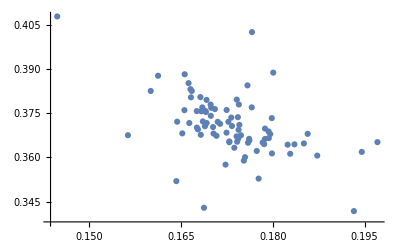

```mathematica
Map[Tooltip[StrikeBallPoint[#[[3]]],{#[[1]],#[[2]]}]&,pitchdata]//ListPlot
```

## TeamsPlayedFor

To get career information on a player in the EventFileYears era, you need to identify the teams he played on.   If you are online, this can be done with just the player's code.  Here is Micky Rivers' career path.  The years from 1970 to 1984 are identified directly from Retrosheet and then rosters for those years are scanned to see which teams the player is listed on.

```mathematica
TeamsPlayedFor["rivem001"]
```

{{rivem001,Mickey Rivers},(1970 | {CAL}
1971 | {CAL}
1972 | {CAL}
1973 | {CAL}
1974 | {CAL}
1975 | {CAL}
1976 | {NYA}
1977 | {NYA}
1978 | {NYA}
1979 | {NYA,TEX}
1980 | {TEX}
1981 | {TEX}
1982 | {TEX}
1983 | {TEX}
1984 | {TEX})}

It takes a while to load in the rosters for a range of years, but they don't have to be reloaded.

```mathematica
TeamsPlayedFor["lowem001",{1990,2008}]//Timing
```

{3.75962,{{lowem001,Mike Lowell},(1998 | {NYA}
1999 | {FLO}
2000 | {FLO}
2001 | {FLO}
2002 | {FLO}
2003 | {FLO}
2004 | {FLO}
2005 | {FLO}
2006 | {BOS}
2007 | {BOS}
2008 | {BOS})}}

After examining rosters from 1990 to 2008 to look for Mike Lowell, it takes almost no time to look for Kenny Lofton.

```mathematica
TeamsPlayedFor["loftk001",{1990,2008}]//Timing
```

{0.013419,{{loftk001,Kenny Lofton},(1991 | {HOU}
1992 | {CLE}
1993 | {CLE}
1994 | {CLE}
1995 | {CLE}
1996 | {CLE}
1997 | {ATL}
1998 | {CLE}
1999 | {CLE}
2000 | {CLE}
2001 | {CLE}
2002 | {CHA,SFN}
2003 | {CHN,PIT}
2004 | {NYA}
2005 | {PHI}
2006 | {LAN}
2007 | {CLE,TEX})}}

Since TeamsPlayedFor reads in many rosters, they can be cleared if memory usage is an issue.

```mathematica
ClearRosters[]
```

## PlayerImport

This function could be used to check calculated stats against stats that are posted on Retrosheet.  Parsing will take some work.  It is currently not in the package.

```mathematica
PlayerImport[code_]:=Import["http://www.retrosheet.org/boxesetc/"<>StringTake[code,1]<>"/P"<>code<>".htm"]
```

```mathematica
PlayerImport[code_,mode_]:=Import["http://www.retrosheet.org/boxesetc/"<>StringTake[code,1]<>"/P"<>code<>".htm",mode]
```

```mathematica
test=PlayerImport["lowem001","TSV"];Take[test,20]
```

(<!DOCTYPE HTML PUBLIC "-//W3C//DTD HTML 4.0//EN" "http://www.w3.org/TR/REC-html40/strict.dtd">
<HTML lang="EN" dir="LTR">
<PRE><A href="../MISC/Pdescr.htm">Read Me</A></PRE>
<HEAD>
<TITLE>Mike Lowell</TITLE>
<link rel="stylesheet" type="text/css" href="http://www.retrosheet.org/menubar/menubar.css">
<script type="text/javascript" src="http://www.retrosheet.org/menubar/menubar.js"></script>
</HEAD>
<BODY>
<p class="nopad"><img src="http://www.retrosheet.org/menubar/retro-logo.gif" alt="Retrosheet" width="400" height="46" class="bancenter"></p>
<div class="mbcenter">
<ul class="nav">
<li><a href="http://www.retrosheet.org/">Home</a></li>
<li><a href="#">About &darr;</a>
<ul>
<li><a href="http://www.retrosheet.org/site.htm">Overview</a></li>
<li><a href="http://www.retrosheet.org/faq.htm">FAQ</a></li>
</ul>
</li>
<li><a href="#">Games/People/Parks &darr;</a>)

(<!DOCTY
PE HTML PUBLIC "-//W3C//DTD HTML 4.0//EN" "http://www.w3.org/TR/REC-html40/strict.dtd">
<HTML lang="EN" dir="LTR">
<PRE><A href="../MISC/Pdescr.htm">Read Me</A></PRE>
<HEAD>
<TITLE>Mike Lowell</TITLE>
<link rel="stylesheet" type="text/css" href="http://www.retrosheet.org/menubar/menubar.css">
<script type="text/javascript" src="http://www.retrosheet.org/menubar/menubar.js"></script>
</HEAD>
<BODY>
<p class="nopad"><img src="http://www.retrosheet.org/menubar/retro-logo.gif" alt="Retrosheet" width="400" height="46" class="bancenter"></p>
<div class="mbcenter">
  <ul class="nav">
    <li><a href="http://www.retrosheet.org/">Home</a></li>
    <li><a href="#">About &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/site.htm">Overview</a></li>
        <li><a href="http://www.retrosheet.org/faq.htm">FAQ</a></li>
      </ul>
    </li>
    <li><a href="#">Games/People/Parks &darr;</a>)

```mathematica
PlayerImport["lowem001","Source"]
```

<!DOCTYPE HTML PUBLIC "-//W3C//DTD HTML 4.0//EN" "http://www.w3.org/TR/REC-html40/strict.dtd">
<HTML lang="EN" dir="LTR">
<PRE><A href="../MISC/Pdescr.htm">Read Me</A></PRE>
<HEAD>
<TITLE>Mike Lowell</TITLE>
<link rel="stylesheet" type="text/css" href="http://www.retrosheet.org/menubar/menubar.css">
<script type="text/javascript" src="http://www.retrosheet.org/menubar/menubar.js"></script>
</HEAD>
<BODY>
<p class="nopad"><img src="http://www.retrosheet.org/menubar/retro-logo.gif" alt="Retrosheet" width="400" height="46" class="bancenter"></p>
<div class="mbcenter">
  <ul class="nav">
    <li><a href="http://www.retrosheet.org/">Home</a></li>
    <li><a href="#">About &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/site.htm">Overview</a></li>
        <li><a href="http://www.retrosheet.org/faq.htm">FAQ</a></li>
      </ul>
    </li>
    <li><a href="#">Games/People/Parks &darr;</a>
      <ul>
        <li><a href="#">People &rarr;</a>
          <ul>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html#Players">Players</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html#Managers">Managers</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html#Coaches">Coaches</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html#Umpires">Umpires</a></li>
            <li><a href="http://www.retrosheet.org/transactions/index.html">Transactions</a></li>
          </ul>
        </li>
        <li><a href="#">Games &rarr;</a>
          <ul>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html">Regular season</a></li>
            <li><a href="http://www.retrosheet.org/Playoff%20Games.htm">Tiebreaker playoffs</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/masterPS.htm">Post-season</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/masterAS.htm">All-Star games</a></li>
          </ul>
        </li>
        <li><a href="#">Places &rarr;</a>
          <ul>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/FRDIR.htm">Franchises</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/PKDIR.htm">Ballparks</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/PNDIR.htm">Birth and death</a></li>
          </ul>
        </li>
        <li><a href="#">Achievements &rarr;</a>
          <ul>
            <li><a href="http://www.retrosheet.org/boxesetc/MISC/XOH.htm">Awards</a></li>
            <li><a href="http://www.retrosheet.org/boxesetc/index.html#TopPerf">Top performances</a></li>
            <li><a href="http://www.retrosheet.org/outstand.htm">No-hitters &amp; cycles</a></li>
            <li><a href="http://www.retrosheet.org/milestones.htm">Milestones</a></li>
          </ul>
        </li>
      </ul>
    </li>
    <li><a href="#">Data downloads &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/game.htm">Play-by-play files</a></li>
        <li><a href="http://www.retrosheet.org/gamelogs/index.html">Game logs</a></li>
        <li><a href="http://www.retrosheet.org/schedule/index.html">Schedules</a></li>
      </ul>
    </li>
    <li><a href="#">Features &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/lists.htm">Noteworthy events</a></li>
        <li><a href="http://www.retrosheet.org/specfeat.htm">Special features</a></li>
        <li><a href="http://www.retrosheet.org/Research/Research.htm">Research papers</a></li>
        <li><a href="http://www.retrosheet.org/wanted/index.html">Most wanted</a></li>
      </ul>
    </li>
    <li><a href="#">Organization &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/history.htm">Who we are</a></li>
        <li><a href="http://groups.yahoo.com/group/RetroList">Discussion group</a></li>
        <li><a href="http://www.retrosheet.org/donation.htm">Donations</a></li>
      </ul>
    </li>
    <li><a href="#">Archives &darr;</a>
      <ul>
        <li><a href="http://www.retrosheet.org/news.htm">Newsletters</a></li>
        <li><a href="http://www.retrosheet.org/archives.htm">Site history</a></li>
      </ul>
    </li>
  </ul>
</div>
<br class="clearboth">

<H2>Mike Lowell</H2>
<TABLE>
<TR><TD>Full name Michael Averett Lowell</TD></TR>
<TR><TD>Born February  24, 1974, <A href="../MISC/PN_202.htm#43">San Juan, Puerto Rico</A></TD></TR>
<TR><TD>First Game: <A href="../1998/B09130NYA1998.htm">September 13, 1998</A>; Final Game: <A href="../2010/B10021BOS2010.htm">October   2, 2010</A></TD></TR>
<TR><TD>Bat: Right    Throw: Right    Height: 6' 4"    Weight: 195</TD></TR>
<TR><TD></TD></TR>
<TR><TD>Named World Series Most Valuable Player (2007)</TD></TR>
<TR><TD>Won NL Gold Glove as third baseman (2005)</TD></TR>
<TR><TD>Named third baseman on The Sporting News NL Silver Slugger Team (2003)</TD></TR>
<TR><TD></TD></TR>
<TR><TD>Ejections: 2002 (1), 2008 (1), 2009 (1). Total: 3</TD></TR><TR><TD><A href="http://sabr.org/bioproj/person/b1f8e16b">SABR Biography</A></TD></TR>
</TABLE>
<PRE><A href="../L/PX_lowem001.htm">Top Performances</A> 
</PRE><PRE><A href="../L/MU0_lowem001.htm">Pitcher Matchups</A>
</PRE><PRE>                           Batting Record
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG   BFW Year Team
<A href="../1998/Y_1998.htm">1998</A> <A href="../1998/TNYA01998.htm">NY  A</A>    <A href="../1998/Ilowem0010011998.htm">Daily</A> <A href="../1998/Jlowem0010011998.htm">Splits</A>    8    15    1    4   0   0   0    0    0   0    1   0   0   0   0   0   0    0   0  .267  .267  .267  -0.2 <A href="../1998/Y_1998.htm">1998</A> <A href="../1998/TNYA01998.htm">NY  A</A>
<A href="../1999/Y_1999.htm">1999</A> <A href="../1999/TFLO01999.htm">FLA N</A>    <A href="../1999/Ilowem0010021999.htm">Daily</A> <A href="../1999/Jlowem0010021999.htm">Splits</A>   97   308   32   78  15   0  12   47   26   1   69   5   0   5   0   0   8    0   0  .253  .317  .419  -0.8 <A href="../1999/Y_1999.htm">1999</A> <A href="../1999/TFLO01999.htm">FLA N</A>
<A href="../2000/Y_2000.htm">2000</A> <A href="../2000/TFLO02000.htm">FLA N</A>    <A href="../2000/Ilowem0010032000.htm">Daily</A> <A href="../2000/Jlowem0010032000.htm">Splits</A>  140   508   73  137  38   0  22   91   54   4   75   9   0  11 <B>  1</B>   4   4    4   0  .270  .344  .474   1.3 <A href="../2000/Y_2000.htm">2000</A> <A href="../2000/TFLO02000.htm">FLA N</A>
<A href="../2001/Y_2001.htm">2001</A> <A href="../2001/TFLO02001.htm">FLA N</A>    <A href="../2001/Ilowem0010042001.htm">Daily</A> <A href="../2001/Jlowem0010042001.htm">Splits</A>  146   551   65  156  37   0  18  100   43   3   79  10   0  10   0   4   9    1   2  .283  .340  .448   1.5 <A href="../2001/Y_2001.htm">2001</A> <A href="../2001/TFLO02001.htm">FLA N</A>
<A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TFLO02002.htm">FLA N</A>    <A href="../2002/Ilowem0010052002.htm">Daily</A> <A href="../2002/Jlowem0010052002.htm">Splits</A>  160   597   88  165  44   0  24   92   65   5   92   4   0 <B> 11</B>   1   5  16    4   3  .276  .346  .471   1.7 <A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TFLO02002.htm">FLA N</A>
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO02003.htm">FLA N</A>    <A href="../2003/Ilowem0010062003.htm">Daily</A> <A href="../2003/Jlowem0010062003.htm">Splits</A>  130   492   76  136  27   1  32  105   56   6   78   3   0   6   0   3  14    3   1  .276  .350  .530   1.9 <A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO02003.htm">FLA N</A>
<A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TFLO02004.htm">FLA N</A>    <A href="../2004/Ilowem0010072004.htm">Daily</A> <A href="../2004/Jlowem0010072004.htm">Splits</A>  158   598   87  175  44   1  27   85   64   8   77   6   0   3   0   7  17    5   1  .293  .365  .505   2.4 <A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TFLO02004.htm">FLA N</A>
<A href="../2005/Y_2005.htm">2005</A> <A href="../2005/TFLO02005.htm">FLA N</A>    <A href="../2005/Ilowem0010082005.htm">Daily</A> <A href="../2005/Jlowem0010082005.htm">Splits</A>  150   500   56  118  36   1   8   58   46   1   58   2   1   9   0   4  14    4   0  .236  .298  .360  -1.6 <A href="../2005/Y_2005.htm">2005</A> <A href="../2005/TFLO02005.htm">FLA N</A>
<A href="../2006/Y_2006.htm">2006</A> <A href="../2006/TBOS02006.htm">BOS A</A>    <A href="../2006/Ilowem0010092006.htm">Daily</A> <A href="../2006/Jlowem0010092006.htm">Splits</A>  153   573   79  163  47   1  20   80   47   5   61   4   0   7   0  10  22    2   2  .284  .339  .475   2.3 <A href="../2006/Y_2006.htm">2006</A> <A href="../2006/TBOS02006.htm">BOS A</A>
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS02007.htm">BOS A</A>    <A href="../2007/Ilowem0010102007.htm">Daily</A> <A href="../2007/Jlowem0010102007.htm">Splits</A>  154   589   79  191  37   2  21  120   53   4   71   3   0   8   0   8  19    3   2  .324  .378  .501   2.3 <A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS02007.htm">BOS A</A>
<A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS02008.htm">BOS A</A>    <A href="../2008/Ilowem0010112008.htm">Daily</A> <A href="../2008/Jlowem0010112008.htm">Splits</A>  113   419   58  115  27   0  17   73   38   2   61   5   0   6   0   5  14    2   2  .274  .338  .461   1.1 <A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS02008.htm">BOS A</A>
<A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS02009.htm">BOS A</A>    <A href="../2009/Ilowem0010122009.htm">Daily</A> <A href="../2009/Jlowem0010122009.htm">Splits</A>  119   445   54  129  29   1  17   75   33   5   61   1   0   5   0   4  24    2   1  .290  .337  .474   0.4 <A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS02009.htm">BOS A</A>
<A href="../2010/Y_2010.htm">2010</A> <A href="../2010/TBOS02010.htm">BOS A</A>    <A href="../2010/Ilowem0010132010.htm">Daily</A> <A href="../2010/Jlowem0010132010.htm">Splits</A>   73   218   23   52  13   0   5   26   23   1   34   0   0   3   0   3   9    0   0  .239  .307  .367  -1.0 <A href="../2010/Y_2010.htm">2010</A> <A href="../2010/TBOS02010.htm">BOS A</A>
Total NL ( 7 Years)         981  3554  477  965 241   3 143  578  354  28  528  39   1  55   2  27  82   21   7  .272  .339  .462   6.4 Total NL
Total AL ( 6 Years)         620  2259  294  654 153   4  80  374  194  17  289  13   0  29   0  30  88    9   7  .290  .345  .467   4.9 Total AL
Total    (13 Years) <A href="../L/Jlowem0010.htm">Splits</A> 1601  5813  771 1619 394   7 223  952  548  45  817  52   1  84   2  57 170   30  14  .279  .342  .464  11.3 Total
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG   BFW Year Team
</PRE><PRE>           Division Series Batting Record
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO22003.htm">FLA N</A>    <A href="../2003/Ilowem0012182003.htm">Daily</A> <A href="../2003/Jlowem0012182003.htm">Splits</A>    2     3    0    0   0   0   0    0    0   0    1   0   0   0   0   0   0    0   0  .000  .000  .000 <A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO22003.htm">FLA N</A>
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS22007.htm">BOS A</A>    <A href="../2007/Ilowem0012202007.htm">Daily</A> <A href="../2007/Jlowem0012202007.htm">Splits</A>    3     9    1    3   2   0   0    3    1   0    0   0   0   1   0   0   1    0   0  .333  .364  .556 <A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS22007.htm">BOS A</A>
<A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS22008.htm">BOS A</A>    <A href="../2008/Ilowem0012242008.htm">Daily</A> <A href="../2008/Jlowem0012242008.htm">Splits</A>    2     8    0    0   0   0   0    0    1   0    3   0   0   0   0   0   0    0   0  .000  .111  .000 <A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS22008.htm">BOS A</A>
<A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS22009.htm">BOS A</A>    <A href="../2009/Ilowem0012252009.htm">Daily</A> <A href="../2009/Jlowem0012252009.htm">Splits</A>    3    10    1    2   0   0   0    1    1   0    0   0   0   0   0   0   1    0   0  .200  .273  .200 <A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS22009.htm">BOS A</A>
Total NL ( 1 Year )           2     3    0    0   0   0   0    0    0   0    1   0   0   0   0   0   0    0   0  .000  .000  .000 Total NL
Total AL ( 3 Years)           8    27    2    5   2   0   0    4    3   0    3   0   0   1   0   0   2    0   0  .185  .258  .259 Total AL
Total    ( 4 Years) <A href="../L/Jlowem0012.htm">Splits</A>   10    30    2    5   2   0   0    4    3   0    4   0   0   1   0   0   2    0   0  .167  .235  .233 Total
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
</PRE><PRE>League Championship Series Batting Record
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO32003.htm">FLA N</A>    <A href="../2003/Ilowem0013172003.htm">Daily</A> <A href="../2003/Jlowem0013172003.htm">Splits</A>    7    20    5    4   0   0   2    3    3   1    4   0   0   0   0   0   0    0   0  .200  .304  .500 <A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO32003.htm">FLA N</A>
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS32007.htm">BOS A</A>    <A href="../2007/Ilowem0013212007.htm">Daily</A> <A href="../2007/Jlowem0013212007.htm">Splits</A>    7    27    3    9   2   0   1    8    2   0    3   1   0   2   0   0   1    0   0  .333  .375  .519 <A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS32007.htm">BOS A</A>
Total NL ( 1 Year )           7    20    5    4   0   0   2    3    3   1    4   0   0   0   0   0   0    0   0  .200  .304  .500 Total NL
Total AL ( 1 Year )           7    27    3    9   2   0   1    8    2   0    3   1   0   2   0   0   1    0   0  .333  .375  .519 Total AL
Total    ( 2 Years) <A href="../L/Jlowem0013.htm">Splits</A>   14    47    8   13   2   0   3   11    5   1    7   1   0   2   0   0   1    0   0  .277  .345  .511 Total
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
</PRE><PRE>              World Series Batting Record
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO42003.htm">FLA N</A>    <A href="../2003/Ilowem0014162003.htm">Daily</A> <A href="../2003/Jlowem0014162003.htm">Splits</A>    6    23    1    5   1   0   0    2    2   0    3   0   0   0   0   0   0    0   0  .217  .280  .261 <A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO42003.htm">FLA N</A>
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS42007.htm">BOS A</A>    <A href="../2007/Ilowem0014222007.htm">Daily</A> <A href="../2007/Jlowem0014222007.htm">Splits</A>    4    15    6    6   3   0   1    4    3   1    1   0   0   0   0   0   0    1   0  .400  .500  .800 <A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS42007.htm">BOS A</A>
Total    ( 2 Years) <A href="../L/Jlowem0014.htm">Splits</A>   10    38    7   11   4   0   1    6    5   1    4   0   0   0   0   0   0    1   0  .289  .372  .474 Total
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
</PRE><PRE>             All-Star Game Batting Record
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
<A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TNLS52002.htm">NL   </A>    <A href="../2002/Ilowem0015142002.htm">Daily</A> <A href="../2002/Jlowem0015142002.htm">Splits</A>    1     3    1    2   0   0   0    0    0   0    0   0   0   0   0   0   0    0   0  .667  .667  .667 <A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TNLS52002.htm">NL   </A>
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TNLS52003.htm">NL   </A>    <A href="../2003/Ilowem0015152003.htm">Daily</A> <A href="../2003/Jlowem0015152003.htm">Splits</A>    1     1    0    1   1   0   0    0    0   0    0   0   0   0   0   0   0    0   0 1.000 1.000 2.000 <A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TNLS52003.htm">NL   </A>
<A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TNLS52004.htm">NL   </A>    <A href="../2004/Ilowem0015192004.htm">Daily</A> <A href="../2004/Jlowem0015192004.htm">Splits</A>    1     2    0    0   0   0   0    0    0   0    1   0   0   0   0   0   0    0   0  .000  .000  .000 <A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TNLS52004.htm">NL   </A>
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TALS52007.htm">AL   </A>    <A href="../2007/Ilowem0015232007.htm">Daily</A> <A href="../2007/Jlowem0015232007.htm">Splits</A>    1     1    1    1   0   0   0    0    0   0    0   0   0   0   0   0   0    0   0 1.000 1.000 1.000 <A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TALS52007.htm">AL   </A>
Total    ( 4 Years) <A href="../L/Jlowem0015.htm">Splits</A>    4     7    2    4   1   0   0    0    0   0    1   0   0   0   0   0   0    0   0  .571  .571  .714 Total
Year Team                     G    AB    R    H  2B  3B  HR  RBI   BB IBB   SO HBP  SH  SF  XI ROE GDP   SB  CS   AVG   OBP   SLG Year Team
</PRE><H1></H1>
<PRE>                           Fielding Record
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
<A href="../1998/Y_1998.htm">1998</A> <A href="../1998/TNYA01998.htm">NY  A</A> <A href="../1998/Mlowem0010011998.htm">Daily</A>  3B    7    3    3    36       2    5    0    1   0 1.000
<A href="../1998/Y_1998.htm">1998</A> <A href="../1998/TNYA01998.htm">NY  A</A>        DH    1    0    0                                      -
<A href="../1999/Y_1999.htm">1999</A> <A href="../1999/TFLO01999.htm">FLA N</A> <A href="../1999/Mlowem0010021999.htm">Daily</A>  3B   83   81   73   716.1    59  143    4   12   0  .981
<A href="../2000/Y_2000.htm">2000</A> <A href="../2000/TFLO02000.htm">FLA N</A> <A href="../2000/Mlowem0010032000.htm">Daily</A>  3B  136  135  130  1191.1   102  260   12   19   0  .968
<A href="../2001/Y_2001.htm">2001</A> <A href="../2001/TFLO02001.htm">FLA N</A> <A href="../2001/Mlowem0010042001.htm">Daily</A>  3B  144  142  135  1250.2 <B>  107</B>  261    9 <B>  35</B>   0  .976
<A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TFLO02002.htm">FLA N</A> <A href="../2002/Mlowem0010052002.htm">Daily</A>  3B <B> 159</B> <B> 159</B>  146 <B> 1400.1</B> <B>  150</B>  286   14   36 <B>  1</B>  .969
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO02003.htm">FLA N</A> <A href="../2003/Mlowem0010062003.htm">Daily</A>  3B  128  128  112  1109.2    84  243    9   27   0 <B> .973</B>
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO02003.htm">FLA N</A>        DH    2    2    2                                      -
<A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TFLO02004.htm">FLA N</A> <A href="../2004/Mlowem0010072004.htm">Daily</A>  3B  154  153  135  1326     117  272    7   30   0  .982
<A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TFLO02004.htm">FLA N</A>        DH    3    3    3                                      -
<A href="../2005/Y_2005.htm">2005</A> <A href="../2005/TFLO02005.htm">FLA N</A> <A href="../2005/Mlowem0010082005.htm">Daily</A>  3B  134  126  119  1118.1   107  243    6 <B>  34</B>   0 <B> .983</B>
<A href="../2005/Y_2005.htm">2005</A> <A href="../2005/TFLO02005.htm">FLA N</A>        2B    8    8    6    67      18   13    1    3   0  .969
<A href="../2006/Y_2006.htm">2006</A> <A href="../2006/TBOS02006.htm">BOS A</A> <A href="../2006/Mlowem0010092006.htm">Daily</A>  3B  153  148  136  1298.2 <B>  143</B>  314    6   39   0  .987
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS02007.htm">BOS A</A> <A href="../2007/Mlowem0010102007.htm">Daily</A>  3B <B> 154</B>  150 <B> 146</B>  1324.1   105  264   15 <B>  34</B>   0  .961
<A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS02008.htm">BOS A</A> <A href="../2008/Mlowem0010112008.htm">Daily</A>  3B  110  108   97   935.2    80  217   10   20   0  .967
<A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS02008.htm">BOS A</A>        DH    2    2    1                                      -
<A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS02009.htm">BOS A</A> <A href="../2009/Mlowem0010122009.htm">Daily</A>  3B  107  105   86   895      82  174    9   14   0  .966
<A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS02009.htm">BOS A</A>        DH    9    8    5                                      -
<A href="../2010/Y_2010.htm">2010</A> <A href="../2010/TBOS02010.htm">BOS A</A> <A href="../2010/Mlowem0010132010.htm">Daily</A>  1B   43   38   28   324     310   24    2   35   0  .994
<A href="../2010/Y_2010.htm">2010</A> <A href="../2010/TBOS02010.htm">BOS A</A>        DH   16   14   12                                      -
<A href="../2010/Y_2010.htm">2010</A> <A href="../2010/TBOS02010.htm">BOS A</A>        3B    4    4    2    32       2    6    0    1   0 1.000
Total (13 Years)  3B 1473 1442 1320 12634.1  1140 2688  101  302   1  .974
Total ( 1 Year )  1B   43   38   28   324     310   24    2   35   0  .994
Total ( 6 Years)  DH   33   29   23                                      -
Total ( 1 Year )  2B    8    8    6    67      18   13    1    3   0  .969
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
</PRE>
<PRE>           Division Series Fielding Record
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO22003.htm">FLA N</A> <A href="../2003/Mlowem0012182003.htm">Daily</A>  3B    2    1    0     7.2     1    2    0    0   0 1.000
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS22007.htm">BOS A</A> <A href="../2007/Mlowem0012202007.htm">Daily</A>  3B    3    3    3    27       3    5    1    0   0  .889
<A href="../2008/Y_2008.htm">2008</A> <A href="../2008/TBOS22008.htm">BOS A</A> <A href="../2008/Mlowem0012242008.htm">Daily</A>  3B    2    2    1    19       3    6    0    0   0 1.000
<A href="../2009/Y_2009.htm">2009</A> <A href="../2009/TBOS22009.htm">BOS A</A> <A href="../2009/Mlowem0012252009.htm">Daily</A>  3B    3    3    2    24       2    9    1    2   0  .917
Total ( 4 Years)  3B   10    9    6    77.2     9   22    2    2   0  .939
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
</PRE>
<PRE>League Championship Series Fielding Record
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO32003.htm">FLA N</A> <A href="../2003/Mlowem0013172003.htm">Daily</A>  3B    7    4    4    44.1     4    8    0    0   0 1.000
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS32007.htm">BOS A</A> <A href="../2007/Mlowem0013212007.htm">Daily</A>  3B    7    7    7    63       5   17    0    1   0 1.000
Total ( 2 Years)  3B   14   11   11   107.1     9   25    0    1   0 1.000
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
</PRE>
<PRE>              World Series Fielding Record
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TFLO42003.htm">FLA N</A> <A href="../2003/Mlowem0014162003.htm">Daily</A>  3B    6    6    6    56       5   11    0    1   0 1.000
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TBOS42007.htm">BOS A</A> <A href="../2007/Mlowem0014222007.htm">Daily</A>  3B    4    4    4    36       2    8    1    0   0  .909
Total ( 2 Years)  3B   10   10   10    92       7   19    1    1   0  .963
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
</PRE>
<PRE>             All-Star Game Fielding Record
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
<A href="../2002/Y_2002.htm">2002</A> <A href="../2002/TNLS52002.htm">NL   </A> <A href="../2002/Mlowem0015142002.htm">Daily</A>  3B    1    0    0     4       0    0    0    0   0     -
<A href="../2003/Y_2003.htm">2003</A> <A href="../2003/TNLS52003.htm">NL   </A> <A href="../2003/Mlowem0015152003.htm">Daily</A>  3B    1    0    0     3       0    1    0    0   0 1.000
<A href="../2004/Y_2004.htm">2004</A> <A href="../2004/TNLS52004.htm">NL   </A> <A href="../2004/Mlowem0015192004.htm">Daily</A>  3B    1    0    0     4       0    0    0    0   0     -
<A href="../2007/Y_2007.htm">2007</A> <A href="../2007/TALS52007.htm">AL   </A> <A href="../2007/Mlowem0015232007.htm">Daily</A>  3B    1    0    0     4       0    0    0    0   0     -
Total ( 4 Years)  3B    4    0    0    15       0    1    0    0   0 1.000
Year Team        POS    G   GS   CG   INN      PO    A  ERR   DP  TP   AVG
</PRE>
<H1></H1>
<PRE>Ejection Information

Date                Team   Umpire              Reason
 8-18-2002     <A href="../2002/B08180FLO2002.htm">BOX</A>  <A href="../2002/TEFLO2002.htm">FLA N</A>  <A href="../T/Ptimmt901.htm">Tim Timmons</A>         Balls and strikes
 7-25-2008     <A href="../2008/B07250BOS2008.htm">BOX</A>  <A href="../2008/TEBOS2008.htm">BOS A</A>  <A href="../F/Pfostm901.htm">Marty Foster</A>        Called third strike
 6- 3-2009     <A href="../2009/B06030DET2009.htm">BOX</A>  <A href="../2009/TEBOS2009.htm">BOS A</A>  <A href="../D/Pdavib902.htm">Bob Davidson</A>        Balls and strikes
</PRE>
<H1></H1>
<PRE>Transaction Information

Selected by <A href="../1995/TM_NYA1995.htm">New York Yankees</A> in the 20th round of the free-agent draft (<A href="../1995/06011995.htm">June 1, 1995</A>
- signed <A href="../1995/06081995.htm">June 8, 1995</A>).

Traded by <A href="../1999/TM_NYA1999.htm">New York Yankees</A> to <A href="../1999/TM_FLO1999.htm">Florida Marlins</A> in exchange for <A href="../J/Pjohnm004.htm">Mark Johnson</A>, Todd
Noel and <A href="../Y/Pyarne001.htm">Ed Yarnall</A> (<A href="../1999/02011999.htm">February 1, 1999</A>).

Traded by <A href="../2005/TM_FLO2005.htm">Florida Marlins</A> with <A href="../B/Pbeckj002.htm">Josh Beckett</A> and <A href="../M/Pmotag001.htm">Guillermo Mota</A> to <A href="../2005/TM_BOS2005.htm">Boston Red Sox</A> in
exchange for <A href="../R/Pramih003.htm">Hanley Ramirez</A>, <A href="../S/Psanca004.htm">Anibal Sanchez</A>, <A href="../G/Pgarch001.htm">Harvey Garcia</A> and <A href="../D/Pdelgj001.htm">Jesus Delgado</A>
(<A href="../2005/11242005.htm">November 24, 2005</A>).

Granted free agency (<A href="../2007/10302007.htm">October 30, 2007</A>).

Signed by <A href="../2007/TM_BOS2007.htm">Boston Red Sox</A> (<A href="../2007/11192007.htm">November 19, 2007</A>).

Granted free agency (<A href="../2010/11012010.htm">November 1, 2010</A>).
</PRE><PRE><A href="../MISC/Pdescr.htm">Read Me</A></PRE>
</BODY></HTML>

```mathematica
PlayerImport["lowem001","Hyperlinks"]
```

{http://www.retrosheet.org/,http://www.retrosheet.org/site.htm,http://www.retrosheet.org/faq.htm,http://www.retrosheet.org/boxesetc/index.html#Players,http://www.retrosheet.org/boxesetc/index.html#Managers,http://www.retrosheet.org/boxesetc/index.html#Coaches,http://www.retrosheet.org/boxesetc/index.html#Umpires,http://www.retrosheet.org/transactions/index.html,http://www.retrosheet.org/boxesetc/index.html,http://www.retrosheet.org/Playoff%20Games.htm,http://www.retrosheet.org/boxesetc/MISC/masterPS.htm,http://www.retrosheet.org/boxesetc/MISC/masterAS.htm,http://www.retrosheet.org/boxesetc/MISC/FRDIR.htm,http://www.retrosheet.org/boxesetc/MISC/PKDIR.htm,http://www.retrosheet.org/boxesetc/MISC/PNDIR.htm,http://www.retrosheet.org/boxesetc/MISC/XOH.htm,http://www.retrosheet.org/boxesetc/index.html#TopPerf,http://www.retrosheet.org/outstand.htm,http://www.retrosheet.org/milestones.htm,http://www.retrosheet.org/game.htm,http://www.retrosheet.org/gamelogs/index.html,http://www.retrosheet.org/schedule/index.html,http://www.retrosheet.org/lists.htm,http://www.retrosheet.org/specfeat.htm,http://www.retrosheet.org/Research/Research.htm,http://www.retrosheet.org/wanted/index.html,http://www.retrosheet.org/history.htm,http://groups.yahoo.com/group/RetroList,http://www.retrosheet.org/donation.htm,http://www.retrosheet.org/news.htm,http://www.retrosheet.org/archives.htm,http://retrosheet.org/boxesetc/MISC/PN_202.htm#43,http://retrosheet.org/boxesetc/1998/B09130NYA1998.htm,http://retrosheet.org/boxesetc/2010/B10021BOS2010.htm,http://sabr.org/bioproj/person/b1f8e16b,http://retrosheet.org/boxesetc/L/PX_lowem001.htm,http://retrosheet.org/boxesetc/L/MU0_lowem001.htm,http://retrosheet.org/boxesetc/1998/Y_1998.htm,http://retrosheet.org/boxesetc/1998/TNYA01998.htm,http://retrosheet.org/boxesetc/1998/Ilowem0010011998.htm,http://retrosheet.org/boxesetc/1998/Jlowem0010011998.htm,http://retrosheet.org/boxesetc/1998/Y_1998.htm,http://retrosheet.org/boxesetc/1998/TNYA01998.htm,http://retrosheet.org/boxesetc/1999/Y_1999.htm,http://retrosheet.org/boxesetc/1999/TFLO01999.htm,http://retrosheet.org/boxesetc/1999/Ilowem0010021999.htm,http://retrosheet.org/boxesetc/1999/Jlowem0010021999.htm,http://retrosheet.org/boxesetc/1999/Y_1999.htm,http://retrosheet.org/boxesetc/1999/TFLO01999.htm,http://retrosheet.org/boxesetc/2000/Y_2000.htm,http://retrosheet.org/boxesetc/2000/TFLO02000.htm,http://retrosheet.org/boxesetc/2000/Ilowem0010032000.htm,http://retrosheet.org/boxesetc/2000/Jlowem0010032000.htm,http://retrosheet.org/boxesetc/2000/Y_2000.htm,http://retrosheet.org/boxesetc/2000/TFLO02000.htm,http://retrosheet.org/boxesetc/2001/Y_2001.htm,http://retrosheet.org/boxesetc/2001/TFLO02001.htm,http://retrosheet.org/boxesetc/2001/Ilowem0010042001.htm,http://retrosheet.org/boxesetc/2001/Jlowem0010042001.htm,http://retrosheet.org/boxesetc/2001/Y_2001.htm,http://retrosheet.org/boxesetc/2001/TFLO02001.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TFLO02002.htm,http://retrosheet.org/boxesetc/2002/Ilowem0010052002.htm,http://retrosheet.org/boxesetc/2002/Jlowem0010052002.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TFLO02002.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO02003.htm,http://retrosheet.org/boxesetc/2003/Ilowem0010062003.htm,http://retrosheet.org/boxesetc/2003/Jlowem0010062003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO02003.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TFLO02004.htm,http://retrosheet.org/boxesetc/2004/Ilowem0010072004.htm,http://retrosheet.org/boxesetc/2004/Jlowem0010072004.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TFLO02004.htm,http://retrosheet.org/boxesetc/2005/Y_2005.htm,http://retrosheet.org/boxesetc/2005/TFLO02005.htm,http://retrosheet.org/boxesetc/2005/Ilowem0010082005.htm,http://retrosheet.org/boxesetc/2005/Jlowem0010082005.htm,http://retrosheet.org/boxesetc/2005/Y_2005.htm,http://retrosheet.org/boxesetc/2005/TFLO02005.htm,http://retrosheet.org/boxesetc/2006/Y_2006.htm,http://retrosheet.org/boxesetc/2006/TBOS02006.htm,http://retrosheet.org/boxesetc/2006/Ilowem0010092006.htm,http://retrosheet.org/boxesetc/2006/Jlowem0010092006.htm,http://retrosheet.org/boxesetc/2006/Y_2006.htm,http://retrosheet.org/boxesetc/2006/TBOS02006.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS02007.htm,http://retrosheet.org/boxesetc/2007/Ilowem0010102007.htm,http://retrosheet.org/boxesetc/2007/Jlowem0010102007.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS02007.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS02008.htm,http://retrosheet.org/boxesetc/2008/Ilowem0010112008.htm,http://retrosheet.org/boxesetc/2008/Jlowem0010112008.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS02008.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS02009.htm,http://retrosheet.org/boxesetc/2009/Ilowem0010122009.htm,http://retrosheet.org/boxesetc/2009/Jlowem0010122009.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS02009.htm,http://retrosheet.org/boxesetc/2010/Y_2010.htm,http://retrosheet.org/boxesetc/2010/TBOS02010.htm,http://retrosheet.org/boxesetc/2010/Ilowem0010132010.htm,http://retrosheet.org/boxesetc/2010/Jlowem0010132010.htm,http://retrosheet.org/boxesetc/2010/Y_2010.htm,http://retrosheet.org/boxesetc/2010/TBOS02010.htm,http://retrosheet.org/boxesetc/L/Jlowem0010.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO22003.htm,http://retrosheet.org/boxesetc/2003/Ilowem0012182003.htm,http://retrosheet.org/boxesetc/2003/Jlowem0012182003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO22003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS22007.htm,http://retrosheet.org/boxesetc/2007/Ilowem0012202007.htm,http://retrosheet.org/boxesetc/2007/Jlowem0012202007.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS22007.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS22008.htm,http://retrosheet.org/boxesetc/2008/Ilowem0012242008.htm,http://retrosheet.org/boxesetc/2008/Jlowem0012242008.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS22008.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS22009.htm,http://retrosheet.org/boxesetc/2009/Ilowem0012252009.htm,http://retrosheet.org/boxesetc/2009/Jlowem0012252009.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS22009.htm,http://retrosheet.org/boxesetc/L/Jlowem0012.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO32003.htm,http://retrosheet.org/boxesetc/2003/Ilowem0013172003.htm,http://retrosheet.org/boxesetc/2003/Jlowem0013172003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO32003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS32007.htm,http://retrosheet.org/boxesetc/2007/Ilowem0013212007.htm,http://retrosheet.org/boxesetc/2007/Jlowem0013212007.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS32007.htm,http://retrosheet.org/boxesetc/L/Jlowem0013.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO42003.htm,http://retrosheet.org/boxesetc/2003/Ilowem0014162003.htm,http://retrosheet.org/boxesetc/2003/Jlowem0014162003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO42003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS42007.htm,http://retrosheet.org/boxesetc/2007/Ilowem0014222007.htm,http://retrosheet.org/boxesetc/2007/Jlowem0014222007.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS42007.htm,http://retrosheet.org/boxesetc/L/Jlowem0014.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TNLS52002.htm,http://retrosheet.org/boxesetc/2002/Ilowem0015142002.htm,http://retrosheet.org/boxesetc/2002/Jlowem0015142002.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TNLS52002.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TNLS52003.htm,http://retrosheet.org/boxesetc/2003/Ilowem0015152003.htm,http://retrosheet.org/boxesetc/2003/Jlowem0015152003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TNLS52003.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TNLS52004.htm,http://retrosheet.org/boxesetc/2004/Ilowem0015192004.htm,http://retrosheet.org/boxesetc/2004/Jlowem0015192004.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TNLS52004.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TALS52007.htm,http://retrosheet.org/boxesetc/2007/Ilowem0015232007.htm,http://retrosheet.org/boxesetc/2007/Jlowem0015232007.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TALS52007.htm,http://retrosheet.org/boxesetc/L/Jlowem0015.htm,http://retrosheet.org/boxesetc/1998/Y_1998.htm,http://retrosheet.org/boxesetc/1998/TNYA01998.htm,http://retrosheet.org/boxesetc/1998/Mlowem0010011998.htm,http://retrosheet.org/boxesetc/1998/Y_1998.htm,http://retrosheet.org/boxesetc/1998/TNYA01998.htm,http://retrosheet.org/boxesetc/1999/Y_1999.htm,http://retrosheet.org/boxesetc/1999/TFLO01999.htm,http://retrosheet.org/boxesetc/1999/Mlowem0010021999.htm,http://retrosheet.org/boxesetc/2000/Y_2000.htm,http://retrosheet.org/boxesetc/2000/TFLO02000.htm,http://retrosheet.org/boxesetc/2000/Mlowem0010032000.htm,http://retrosheet.org/boxesetc/2001/Y_2001.htm,http://retrosheet.org/boxesetc/2001/TFLO02001.htm,http://retrosheet.org/boxesetc/2001/Mlowem0010042001.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TFLO02002.htm,http://retrosheet.org/boxesetc/2002/Mlowem0010052002.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO02003.htm,http://retrosheet.org/boxesetc/2003/Mlowem0010062003.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO02003.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TFLO02004.htm,http://retrosheet.org/boxesetc/2004/Mlowem0010072004.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TFLO02004.htm,http://retrosheet.org/boxesetc/2005/Y_2005.htm,http://retrosheet.org/boxesetc/2005/TFLO02005.htm,http://retrosheet.org/boxesetc/2005/Mlowem0010082005.htm,http://retrosheet.org/boxesetc/2005/Y_2005.htm,http://retrosheet.org/boxesetc/2005/TFLO02005.htm,http://retrosheet.org/boxesetc/2006/Y_2006.htm,http://retrosheet.org/boxesetc/2006/TBOS02006.htm,http://retrosheet.org/boxesetc/2006/Mlowem0010092006.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS02007.htm,http://retrosheet.org/boxesetc/2007/Mlowem0010102007.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS02008.htm,http://retrosheet.org/boxesetc/2008/Mlowem0010112008.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS02008.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS02009.htm,http://retrosheet.org/boxesetc/2009/Mlowem0010122009.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS02009.htm,http://retrosheet.org/boxesetc/2010/Y_2010.htm,http://retrosheet.org/boxesetc/2010/TBOS02010.htm,http://retrosheet.org/boxesetc/2010/Mlowem0010132010.htm,http://retrosheet.org/boxesetc/2010/Y_2010.htm,http://retrosheet.org/boxesetc/2010/TBOS02010.htm,http://retrosheet.org/boxesetc/2010/Y_2010.htm,http://retrosheet.org/boxesetc/2010/TBOS02010.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO22003.htm,http://retrosheet.org/boxesetc/2003/Mlowem0012182003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS22007.htm,http://retrosheet.org/boxesetc/2007/Mlowem0012202007.htm,http://retrosheet.org/boxesetc/2008/Y_2008.htm,http://retrosheet.org/boxesetc/2008/TBOS22008.htm,http://retrosheet.org/boxesetc/2008/Mlowem0012242008.htm,http://retrosheet.org/boxesetc/2009/Y_2009.htm,http://retrosheet.org/boxesetc/2009/TBOS22009.htm,http://retrosheet.org/boxesetc/2009/Mlowem0012252009.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO32003.htm,http://retrosheet.org/boxesetc/2003/Mlowem0013172003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS32007.htm,http://retrosheet.org/boxesetc/2007/Mlowem0013212007.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TFLO42003.htm,http://retrosheet.org/boxesetc/2003/Mlowem0014162003.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TBOS42007.htm,http://retrosheet.org/boxesetc/2007/Mlowem0014222007.htm,http://retrosheet.org/boxesetc/2002/Y_2002.htm,http://retrosheet.org/boxesetc/2002/TNLS52002.htm,http://retrosheet.org/boxesetc/2002/Mlowem0015142002.htm,http://retrosheet.org/boxesetc/2003/Y_2003.htm,http://retrosheet.org/boxesetc/2003/TNLS52003.htm,http://retrosheet.org/boxesetc/2003/Mlowem0015152003.htm,http://retrosheet.org/boxesetc/2004/Y_2004.htm,http://retrosheet.org/boxesetc/2004/TNLS52004.htm,http://retrosheet.org/boxesetc/2004/Mlowem0015192004.htm,http://retrosheet.org/boxesetc/2007/Y_2007.htm,http://retrosheet.org/boxesetc/2007/TALS52007.htm,http://retrosheet.org/boxesetc/2007/Mlowem0015232007.htm,http://retrosheet.org/boxesetc/2002/B08180FLO2002.htm,http://retrosheet.org/boxesetc/2002/TEFLO2002.htm,http://retrosheet.org/boxesetc/T/Ptimmt901.htm,http://retrosheet.org/boxesetc/2008/B07250BOS2008.htm,http://retrosheet.org/boxesetc/2008/TEBOS2008.htm,http://retrosheet.org/boxesetc/F/Pfostm901.htm,http://retrosheet.org/boxesetc/2009/B06030DET2009.htm,http://retrosheet.org/boxesetc/2009/TEBOS2009.htm,http://retrosheet.org/boxesetc/D/Pdavib902.htm,http://retrosheet.org/boxesetc/1995/TM_NYA1995.htm,http://retrosheet.org/boxesetc/1995/06011995.htm,http://retrosheet.org/boxesetc/1995/06081995.htm,http://retrosheet.org/boxesetc/1999/TM_NYA1999.htm,http://retrosheet.org/boxesetc/1999/TM_FLO1999.htm,http://retrosheet.org/boxesetc/J/Pjohnm004.htm,http://retrosheet.org/boxesetc/Y/Pyarne001.htm,http://retrosheet.org/boxesetc/1999/02011999.htm,http://retrosheet.org/boxesetc/2005/TM_FLO2005.htm,http://retrosheet.org/boxesetc/B/Pbeckj002.htm,http://retrosheet.org/boxesetc/M/Pmotag001.htm,http://retrosheet.org/boxesetc/2005/TM_BOS2005.htm,http://retrosheet.org/boxesetc/R/Pramih003.htm,http://retrosheet.org/boxesetc/S/Psanca004.htm,http://retrosheet.org/boxesetc/G/Pgarch001.htm,http://retrosheet.org/boxesetc/D/Pdelgj001.htm,http://retrosheet.org/boxesetc/2005/11242005.htm,http://retrosheet.org/boxesetc/2007/10302007.htm,http://retrosheet.org/boxesetc/2007/TM_BOS2007.htm,http://retrosheet.org/boxesetc/2007/11192007.htm,http://retrosheet.org/boxesetc/2010/11012010.htm,http://retrosheet.org/boxesetc/MISC/Pdescr.htm}

## More Parsing of Plays

In the original PlayerAtBats, each at-bat was a list of four items, the game ID, inning/half, pitcher and play.    I realized that the play data had the inning in it, so the second item could be removed.  Also, listing the pitcher was time consuming, so that is now an option, with the pitcher in an at-bat being listed last.

```mathematica
temp=AllEvents["BOS",2007]
```

{BOS @ KCA on 2007/04/02,BOS @ KCA on 2007/04/04,BOS @ KCA on 2007/04/05,BOS @ TEX on 2007/04/06,BOS @ TEX on 2007/04/07,BOS @ TEX on 2007/04/08,SEA @ BOS on 2007/04/10,SEA @ BOS on 2007/04/11,ANA @ BOS on 2007/04/13,ANA @ BOS on 2007/04/14,ANA @ BOS on 2007/04/16,BOS @ TOR on 2007/04/17,BOS @ TOR on 2007/04/18,BOS @ TOR on 2007/04/19,NYA @ BOS on 2007/04/20,NYA @ BOS on 2007/04/21,NYA @ BOS on 2007/04/22,TOR @ BOS on 2007/04/23,TOR @ BOS on 2007/04/24,BOS @ BAL on 2007/04/25,BOS @ BAL on 2007/04/26,BOS @ NYA on 2007/04/27,BOS @ NYA on 2007/04/28,BOS @ NYA on 2007/04/29,OAK @ BOS on 2007/05/01,OAK @ BOS on 2007/05/02,SEA @ BOS on 2007/05/03,BOS @ MIN on 2007/05/04,BOS @ MIN on 2007/05/05,BOS @ MIN on 2007/05/06,BOS @ TOR on 2007/05/08,BOS @ TOR on 2007/05/09,BOS @ TOR on 2007/05/10,BAL @ BOS on 2007/05/11,BAL @ BOS on 2007/05/12,BAL @ BOS on 2007/05/13,DET @ BOS on 2007/05/14,DET @ BOS on 2007/05/15,DET @ BOS on 2007/05/17,DET @ BOS on 2007/05/17,ATL @ BOS on 2007/05/19,ATL @ BOS on 2007/05/19,ATL @ BOS on 2007/05/20,BOS @ NYA on 2007/05/21,BOS @ NYA on 2007/05/22,BOS @ NYA on 2007/05/23,BOS @ TEX on 2007/05/25,BOS @ TEX on 2007/05/26,BOS @ TEX on 2007/05/27,CLE @ BOS on 2007/05/28,CLE @ BOS on 2007/05/29,CLE @ BOS on 2007/05/30,NYA @ BOS on 2007/06/01,NYA @ BOS on 2007/06/02,NYA @ BOS on 2007/06/03,BOS @ OAK on 2007/06/04,BOS @ OAK on 2007/06/05,BOS @ OAK on 2007/06/06,BOS @ OAK on 2007/06/07,BOS @ ARI on 2007/06/08,BOS @ ARI on 2007/06/09,BOS @ ARI on 2007/06/10,COL @ BOS on 2007/06/12,COL @ BOS on 2007/06/13,COL @ BOS on 2007/06/14,SFN @ BOS on 2007/06/15,SFN @ BOS on 2007/06/16,SFN @ BOS on 2007/06/17,BOS @ ATL on 2007/06/18,BOS @ ATL on 2007/06/19,BOS @ ATL on 2007/06/20,BOS @ SDN on 2007/06/22,BOS @ SDN on 2007/06/23,BOS @ SDN on 2007/06/24,BOS @ SEA on 2007/06/25,BOS @ SEA on 2007/06/26,BOS @ SEA on 2007/06/27,TEX @ BOS on 2007/06/29,TEX @ BOS on 2007/06/30,TEX @ BOS on 2007/07/01,TEX @ BOS on 2007/07/02,TBA @ BOS on 2007/07/03,TBA @ BOS on 2007/07/04,TBA @ BOS on 2007/07/05,BOS @ DET on 2007/07/06,BOS @ DET on 2007/07/07,BOS @ DET on 2007/07/08,TOR @ BOS on 2007/07/12,TOR @ BOS on 2007/07/13,TOR @ BOS on 2007/07/14,TOR @ BOS on 2007/07/15,KCA @ BOS on 2007/07/16,KCA @ BOS on 2007/07/17,KCA @ BOS on 2007/07/18,CHA @ BOS on 2007/07/19,CHA @ BOS on 2007/07/20,CHA @ BOS on 2007/07/21,CHA @ BOS on 2007/07/22,BOS @ CLE on 2007/07/23,BOS @ CLE on 2007/07/24,BOS @ CLE on 2007/07/25,BOS @ CLE on 2007/07/26,BOS @ TBA on 2007/07/27,BOS @ TBA on 2007/07/28,BOS @ TBA on 2007/07/29,BAL @ BOS on 2007/07/31,BAL @ BOS on 2007/08/01,BAL @ BOS on 2007/08/02,BOS @ SEA on 2007/08/03,BOS @ SEA on 2007/08/04,BOS @ SEA on 2007/08/05,BOS @ ANA on 2007/08/06,BOS @ ANA on 2007/08/07,BOS @ ANA on 2007/08/08,BOS @ BAL on 2007/08/10,BOS @ BAL on 2007/08/11,BOS @ BAL on 2007/08/12,TBA @ BOS on 2007/08/13,TBA @ BOS on 2007/08/14,TBA @ BOS on 2007/08/15,ANA @ BOS on 2007/08/17,ANA @ BOS on 2007/08/17,ANA @ BOS on 2007/08/18,ANA @ BOS on 2007/08/19,BOS @ TBA on 2007/08/20,BOS @ TBA on 2007/08/21,BOS @ TBA on 2007/08/22,BOS @ CHA on 2007/08/24,BOS @ CHA on 2007/08/24,BOS @ CHA on 2007/08/25,BOS @ CHA on 2007/08/26,BOS @ NYA on 2007/08/28,BOS @ NYA on 2007/08/29,BOS @ NYA on 2007/08/30,BAL @ BOS on 2007/08/31,BAL @ BOS on 2007/09/01,BAL @ BOS on 2007/09/02,TOR @ BOS on 2007/09/03,TOR @ BOS on 2007/09/04,TOR @ BOS on 2007/09/05,BOS @ BAL on 2007/09/06,BOS @ BAL on 2007/09/07,BOS @ BAL on 2007/09/08,BOS @ BAL on 2007/09/09,TBA @ BOS on 2007/09/10,TBA @ BOS on 2007/09/11,TBA @ BOS on 2007/09/12,NYA @ BOS on 2007/09/14,NYA @ BOS on 2007/09/15,NYA @ BOS on 2007/09/16,BOS @ TOR on 2007/09/17,BOS @ TOR on 2007/09/18,BOS @ TOR on 2007/09/19,BOS @ TBA on 2007/09/21,BOS @ TBA on 2007/09/22,BOS @ TBA on 2007/09/23,OAK @ BOS on 2007/09/25,OAK @ BOS on 2007/09/26,MIN @ BOS on 2007/09/27,MIN @ BOS on 2007/09/28,MIN @ BOS on 2007/09/29,MIN @ BOS on 2007/09/30}

```mathematica
FromPlayerCode["ramim002"]
```

Manny Ramirez

Manny's opening day at-bats in 2007.

```mathematica
PlayerAtBats["ramim002",temp[[1]]]
```

(KCA200704020 | play(1,0,ramim002,11,BCX,8/F)
KCA200704020 | play(4,0,ramim002,20,BBX,53/G)
KCA200704020 | play(6,0,ramim002,20,BBX,64(1)3/GDP)
KCA200704020 | play(9,0,ramim002,12,SSBC,K))

Default is to not include the pitchers.

```mathematica
Options[PlayerAtBats]
```

{WithPitchers→False}

```mathematica
PlayerAtBats["ramim002",temp[[1]],WithPitchers->True]
```

(KCA200704020 | play(1,0,ramim002,11,BCX,8/F) | mechg001
KCA200704020 | play(4,0,ramim002,20,BBX,53/G) | mechg001
KCA200704020 | play(6,0,ramim002,20,BBX,64(1)3/GDP) | mechg001
KCA200704020 | play(9,0,ramim002,12,SSBC,K) | peraj002)

HitSafelyQ identifies whether a player hit safely in a game.  More on this later.

```mathematica
HitSafelyQ["ramim002",temp[[1]]]
```

False

As can be seen from these two timings, the inclusion of pitchers takes a lot more time.  I'm sure it could be sped up by revisiting the code as some point.

```mathematica
(mannyAtBats07=PlayerAtBats["ramim002",#]&/@temp;)//Timing
```

{0.100892,Null}

```mathematica
(mannyAtBats07WithPitchers=PlayerAtBats["ramim002",#,WithPitchers->True]&/@temp;)//Timing
```

{13.3389,Null}

## Ballpark, Team and League Information

#### Ballparks

```mathematica
{ParkCITY[#]}&/@BallparkData//Sequence@@#&//Union
```

{Albany,Altoona,Anaheim,Arlington,Atlanta,Baltimore,Bloomington,Boston,Brooklyn,Buffalo,Canton,Chicago,Cincinnati,Cleveland,Collinwood,Columbus,Covington,Dayton,Denver,Detroit,Dover,Elmira,Fort Wayne,Geauga Lake,Gloucester City,Grand Rapids,Greenbush (Rensselaer),Harrison,Hartford,Hoboken,Honolulu,Houston,Indianapolis,Irondequoit,Jersey City,Kansas City,Keokuk,Lake Buena Vista,Las Vegas,Los Angeles,Louisville,Ludlow,Maspeth,Miami,Middletown,Milwaukee,Minneapolis,Monterrey,Montreal,Newark,New Haven,New York,Oakland,Philadelphia,Phoenix,Pittsburgh,Providence,Richmond,Rochester,Rockford,San Diego,San Francisco,San Juan,Seattle,Springfield,St. George,St. Louis,St. Petersburg,Syracuse,Three Rivers,Tokyo,Toledo,Toronto,Troy,Warwick,Washington,Watervliet,Waverly,Weehawken,West New York,Wheeling,Wilmington,Worcester}

Major League parks located in Massachusetts.

```mathematica
Select[BallparkData,ParkSTATE[#]=="MA"&]
```

(ALB01 | Riverside Park |  | Albany | NY | 09/11/1880 | 05/18/1882 | NL | TRN:9/11/80;6/15&9/10/1881;5/16-5/18/1882
ALB02 | Greenbush Grounds |  | Greenbush (Rensselaer) | NY | 05/30/1882 | 05/30/1882 | NL | TRN:5/30/1882(1);Game 2 at TRO02
BUF01 | Riverside Grounds |  | Buffalo | NY | 05/01/1879 | 09/08/1883 | NL | 
BUF02 | Olympic Park I |  | Buffalo | NY | 05/21/1884 | 10/07/1885 | NL | 
BUF03 | Olympic Park II |  | Buffalo | NY | 04/19/1890 | 10/04/1890 | PL | 
BUF04 | Federal League Park |  | Buffalo | NY | 05/11/1914 | 09/29/1915 | FL | 
ELM01 | Maple Avenue Driving Park |  | Elmira | NY | 10/10/1885 | 10/10/1885 | NL | BFN
IRO01 | Windsor Beach |  | Irondequoit | NY | 05/11/1890 | 07/20/1890 | AA | RC2: Sundays
MAS01 | Long Island Grounds |  | Maspeth | NY | 07/27/1890 | 08/03/1890 | AA | BR4: 2 games
NYC01 | Union Grounds |  | Brooklyn | NY | 05/09/1871 | 09/21/1877 |  | NY2:1871-75;BR1:1872;BR2:1873-75;NY3:1876;HAR:1877
NYC02 | Capitoline Grounds |  | Brooklyn | NY | 05/06/1872 | 10/09/1872 | NA | BR2
NYC03 | Polo Grounds I (Southeast Diamond) |  | New York | NY | 05/01/1883 | 10/13/1888 |  | NY1:1883-88; NY4:7/17/1884-1885
NYC04 | Polo Grounds II (Southwest Diamond) |  | New York | NY | 05/30/1883 | 10/25/1883 | AA | 
NYC05 | Washington Park I |  | Brooklyn | NY | 05/05/1884 | 05/04/1889 | AA | BR3
NYC06 | Metropolitan Park |  | New York | NY | 05/13/1884 | 08/23/1884 | AA | 
NYC07 | Grauer's Ridgewood Park | Ridgewood Park I | New York | NY | 05/02/1886 | 09/19/1886 | AA | BR3: Sundays
NYC08 | Washington Park II |  | Brooklyn | NY | 05/30/1889 | 10/03/1890 |  | BR3:1889; BRO:1890
NYC09 | Polo Grounds III |  | New York | NY | 07/08/1889 | 09/13/1890 | NL | 
NYC10 | Polo Grounds IV |  | New York | NY | 04/19/1890 | 04/13/1911 |  | NYP:1890; NY1:1891-1911
NYC11 | Eastern Park |  | Brooklyn | NY | 04/28/1890 | 10/02/1897 |  | BRP:1890; BRO:1891-97
NYC12 | Washington Park III |  | Brooklyn | NY | 04/30/1898 | 10/05/1912 | NL |  
NYC13 | Hilltop Park |  | New York | NY | 04/30/1903 | 10/05/1912 |  | NYA:1903-1912; NY1: 4/15 to 5/30/1911
NYC14 | Polo Grounds V |  | New York | NY | 06/28/1911 | 09/18/1963 |  | NY1:1911-1957;NYA:1913-1922;NYN:1962-63
NYC15 | Ebbets Field |  | Brooklyn | NY | 04/09/1913 | 09/24/1957 | NL | 
NYC16 | Yankee Stadium I |  | New York | NY | 04/18/1923 | 09/21/2008 | AL | no games 1974-75
NYC17 | Shea Stadium | William A. Shea Stadium | New York | NY | 04/17/1964 | 09/28/2008 | NL | NYN:1964-2008; NYA:1974-75
NYC18 | Wallace's Ridgewood Park | Ridgewood Park II | New York | NY | 04/24/1887 | 06/08/1890 | AA | BR3: Sundays (1887-1889); BR4: 1890
NYC19 | Washington Park IV |  | Brooklyn | NY | 05/11/1914 | 09/30/1915 | FL | BRF
NYC20 | Citi Field |  | New York | NY | 04/13/2009 |  | NL | 
NYC21 | Yankee Stadium II |  | New York | NY | 04/16/2009 |  | AL | 
ROC01 | Culver Field I |  | Rochester | NY | 04/28/1890 | 10/06/1890 | AA | 
ROC02 | Culver Field II |  | Rochester | NY | 08/27/1898 | 08/29/1898 | NL | CL4: 2 games
ROC03 | Ontario Beach Grounds |  | Rochester | NY | 08/28/1898 | 08/28/1898 | NL | CL4
SAI01 | St. George Cricket Grounds |  | St. George | NY | 04/22/1886 | 06/14/1889 |  | NY4:1886-87; NY1:4/29 to 6/14/1889
SYR01 | Star Park I | Newell Park | Syracuse | NY | 05/28/1879 | 09/10/1879 | NL | 
SYR02 | Star Park II |  | Syracuse | NY | 04/28/1890 | 10/06/1890 | AA | 
SYR03 | Iron Pier |  | Syracuse | NY | 08/03/1890 | 08/03/1890 | AA | Forfeit by LS2 to SR2; no game ever played here
THR01 | Three Rivers Park |  | Three Rivers | NY | 05/18/1890 | 07/20/1890 | AA | SR2: Sundays
TRO01 | Haymakers' Grounds |  | Troy | NY | 05/09/1871 | 09/30/1881 |  | TRO:1871-72; TRN: 1880-81
TRO02 | Putnam Grounds |  | Troy | NY | 05/28/1879 | 05/30/1882 | NL | 
WAT01 | Troy Ball Club Grounds |  | Watervliet | NY | 05/20/1882 | 08/26/1882 | NL | TRN)

"New" ballparks of the 1950's.  None are still active.

```mathematica
Select[BallparkData,ParkSTART[#][[1]]≥1950&&ParkSTART[#][[1]]≤1959&]
```

(BAL11 | Memorial Stadium |  | Baltimore | MD | 04/15/1954 | 09/30/1991 | AL | 
JER02 | Roosevelt Stadium |  | Jersey City | NJ | 04/19/1956 | 09/03/1957 | NL | BRO: 7 gms (1956) & 8 gms (1957)
KAN05 | Municipal Stadium |  | Kansas City | MO | 04/12/1955 | 10/04/1972 | AL | KC1:1955-67; KCA:1969-1972
LOS01 | Los Angeles Memorial Coliseum |  | Los Angeles | CA | 04/18/1958 | 09/20/1961 | NL | 
MIL05 | County Stadium |  | Milwaukee | WI | 04/14/1953 | 09/28/2000 |  | MLN:1953-65; CHA:9gms(1968)&11gms(1969);MIL:70-00
SFO01 | Seals Stadium |  | San Francisco | CA | 04/15/1958 | 09/20/1959 | NL | )

Ballparks that were retired in the 1910's

```mathematica
Select[BallparkData,ParkEND[#][[1]]≥1910&&ParkEND[#][[1]]≤1919&]
```

(BAL10 | Terrapin Park | Oriole Park V | Baltimore | MD | 04/13/1914 | 10/02/1915 | FL | 
BOS05 | South End Grounds III |  | Boston | MA | 07/20/1894 | 08/11/1914 | NL | 
BOS06 | Huntington Avenue Baseball Grounds |  | Boston | MA | 05/08/1901 | 10/07/1911 | AL | 
BUF04 | Federal League Park |  | Buffalo | NY | 05/11/1914 | 09/29/1915 | FL | 
CHI08 | West Side Grounds |  | Chicago | IL | 05/13/1893 | 10/03/1915 | NL | CHN:1893(Sun);1894-1915
CHI09 | South Side Park III |  | Chicago | IL | 04/24/1901 | 06/27/1910 | AL | 
CIN06 | Palace of the Fans | League Park III | Cincinnati | OH | 04/17/1902 | 10/06/1911 | NL | 
DET02 | Bennett Park |  | Detroit | MI | 04/25/1901 | 09/10/1911 | AL | 
HAR01 | Harrison Field |  | Harrison | NJ | 04/16/1915 | 10/03/1915 | FL | NEW
IND07 | Federal League Park | Washington Park | Indianapolis | IN | 04/23/1914 | 10/08/1914 | FL | 
KAN04 | Gordon and Koppel Field |  | Kansas City | MO | 04/16/1914 | 09/28/1915 | FL | 
NYC10 | Polo Grounds IV |  | New York | NY | 04/19/1890 | 04/13/1911 |  | NYP:1890; NY1:1891-1911
NYC12 | Washington Park III |  | Brooklyn | NY | 04/30/1898 | 10/05/1912 | NL |  
NYC13 | Hilltop Park |  | New York | NY | 04/30/1903 | 10/05/1912 |  | NYA:1903-1912; NY1: 4/15 to 5/30/1911
NYC19 | Washington Park IV |  | Brooklyn | NY | 05/11/1914 | 09/30/1915 | FL | BRF
PIT05 | Exposition Park III |  | Pittsburgh | PA | 04/19/1890 | 10/02/1915 |  | PTP:1890; PIT:1891-6/29/1909; PTF:1914-15
STL08 | Handlan's Park | Federal League Park | St. Louis | MO | 04/16/1914 | 10/03/1915 | FL | 
WAS08 | American League Park II |  | Washington | DC | 04/14/1904 | 10/06/1910 | AL | )

```mathematica
ParkID["Miller Park"]
```

{MIL06}

```mathematica
ParkRecord[First[ParkID["Miller Park"]]]
```

{MIL06,Miller Park,,Milwaukee,WI,04/06/2001,,NL,}

In 1961, what ballparks did Roger Maris hit his home runs?

```mathematica
ParkID[g_retrogame] := g /. {retrogame[__, info["site", id_], __] -> id}
```

```mathematica
{ParkID[#],
List@@Select[Select[#,(Result[#]=="HR")&],(#[[3]]=="marir101")&]}&/@AllEvents["NYA",1961]//Select[#,Last[#]≠{}&]&//Sort//Split[#,First[#1]==First[#2]&]&//Map[{ParkRecord[First[First[#]]]//{#[[2]],#[[4]],#[[5]]}&,Length[Flatten[Last[Transpose[#]]]]}&,#]&
```

({Memorial Stadium,Baltimore,MD} | 1
{Fenway Park,Boston,MA} | 4
{Comiskey Park I,Chicago,IL} | 5
{Cleveland Stadium,Cleveland,OH} | 5
{Tiger Stadium,Detroit,MI} | 5
{Municipal Stadium,Kansas City,MO} | 4
{Wrigley Field,Los Angeles,CA} | 2
{Metropolitan Stadium,Bloomington,MN} | 1
{Yankee Stadium I,New York,NY} | 30
{Griffith Stadium,Washington,DC} | 4)

#### Teams, Leagues and Divisions.

```mathematica
Teams[1988]
```

(MIL | MIL | AL | E | Milwaukee | Brewers |  | 4/15/1972 | 10/3/1993 | Milwaukee | WI
TEX | TEX | AL | W | Texas | Rangers |  | 4/15/1972 |  | Arlington | TX
SEA | SEA | AL | W | Seattle | Mariners |  | 4/6/1977 |  | Seattle | WA
MIN | MIN | AL | W | Minnesota | Twins |  | 4/6/1982 | 10/3/1993 | Minneapolis | MN
ATL | ATL | NL | W | Atlanta | Braves |  | 4/7/1969 | 10/3/1993 | Atlanta | GA
CIN | CIN | NL | W | Cincinnati | Reds |  | 4/7/1969 | 10/3/1993 | Cincinnati | OH
LAN | LAN | NL | W | Los Angeles | Dodgers |  | 4/7/1969 |  | Los Angeles | CA
NYA | NYA | AL | E | New York | Yankees |  | 4/7/1969 |  | New York | NY
SFN | SFN | NL | W | San Francisco | Giants |  | 4/7/1969 |  | San Francisco | CA
TOR | TOR | AL | E | Toronto | Blue Jays |  | 4/7/1977 |  | Toronto | ON
ANA | CAL | AL | W | California | Angels |  | 4/8/1969 | 9/29/1996 | Anaheim | CA
BAL | BAL | AL | E | Baltimore | Orioles |  | 4/8/1969 |  | Baltimore | MD
BOS | BOS | AL | E | Boston | Red Sox |  | 4/8/1969 |  | Boston | MA
CHA | CHA | AL | W | Chicago | White Sox |  | 4/8/1969 | 10/3/1993 | Chicago | IL
CHN | CHN | NL | E | Chicago | Cubs |  | 4/8/1969 | 10/3/1993 | Chicago | IL
CLE | CLE | AL | E | Cleveland | Indians |  | 4/8/1969 | 10/3/1993 | Cleveland | OH
DET | DET | AL | E | Detroit | Tigers |  | 4/8/1969 | 9/28/1997 | Detroit | MI
HOU | HOU | NL | W | Houston | Astros |  | 4/8/1969 | 10/3/1993 | Houston | TX
KCA | KCA | AL | W | Kansas City | Royals |  | 4/8/1969 | 10/3/1993 | Kansas City | MO
NYN | NYN | NL | E | New York | Mets |  | 4/8/1969 |  | New York | NY
OAK | OAK | AL | W | Oakland | Athletics | A's | 4/8/1969 |  | Oakland | CA
PHI | PHI | NL | E | Philadelphia | Phillies |  | 4/8/1969 |  | Philadelphia | PA
PIT | PIT | NL | E | Pittsburgh | Pirates |  | 4/8/1969 | 10/3/1993 | Pittsburgh | PA
SDN | SDN | NL | W | San Diego | Padres |  | 4/8/1969 |  | San Diego | CA
SLN | SLN | NL | E | St. Louis | Cardinals |  | 4/8/1969 | 10/3/1993 | St. Louis | MO
WAS | MON | NL | E | Montreal | Expos |  | 4/8/1969 | 10/3/2004 | Montreal | QC)

```mathematica
Leagues[1988]
```

{AL,NL}

```mathematica
Teams[1988,"AL"]
```

(MIL | MIL | AL | E | Milwaukee | Brewers |  | 4/15/1972 | 10/3/1993 | Milwaukee | WI
TEX | TEX | AL | W | Texas | Rangers |  | 4/15/1972 |  | Arlington | TX
SEA | SEA | AL | W | Seattle | Mariners |  | 4/6/1977 |  | Seattle | WA
MIN | MIN | AL | W | Minnesota | Twins |  | 4/6/1982 | 10/3/1993 | Minneapolis | MN
NYA | NYA | AL | E | New York | Yankees |  | 4/7/1969 |  | New York | NY
TOR | TOR | AL | E | Toronto | Blue Jays |  | 4/7/1977 |  | Toronto | ON
ANA | CAL | AL | W | California | Angels |  | 4/8/1969 | 9/29/1996 | Anaheim | CA
BAL | BAL | AL | E | Baltimore | Orioles |  | 4/8/1969 |  | Baltimore | MD
BOS | BOS | AL | E | Boston | Red Sox |  | 4/8/1969 |  | Boston | MA
CHA | CHA | AL | W | Chicago | White Sox |  | 4/8/1969 | 10/3/1993 | Chicago | IL
CLE | CLE | AL | E | Cleveland | Indians |  | 4/8/1969 | 10/3/1993 | Cleveland | OH
DET | DET | AL | E | Detroit | Tigers |  | 4/8/1969 | 9/28/1997 | Detroit | MI
KCA | KCA | AL | W | Kansas City | Royals |  | 4/8/1969 | 10/3/1993 | Kansas City | MO
OAK | OAK | AL | W | Oakland | Athletics | A's | 4/8/1969 |  | Oakland | CA)

```mathematica
Teams[1988,{"AL","W"}]
```

(TEX | TEX | AL | W | Texas | Rangers |  | 4/15/1972 |  | Arlington | TX
SEA | SEA | AL | W | Seattle | Mariners |  | 4/6/1977 |  | Seattle | WA
MIN | MIN | AL | W | Minnesota | Twins |  | 4/6/1982 | 10/3/1993 | Minneapolis | MN
ANA | CAL | AL | W | California | Angels |  | 4/8/1969 | 9/29/1996 | Anaheim | CA
CHA | CHA | AL | W | Chicago | White Sox |  | 4/8/1969 | 10/3/1993 | Chicago | IL
KCA | KCA | AL | W | Kansas City | Royals |  | 4/8/1969 | 10/3/1993 | Kansas City | MO
OAK | OAK | AL | W | Oakland | Athletics | A's | 4/8/1969 |  | Oakland | CA)

```mathematica
Divisions[1988]
```

(AL | E
AL | W
NL | E
NL | W)

```mathematica
Map[Teams[1988,#]&,Divisions[1988]]
```

{(MIL | MIL | AL | E | Milwaukee | Brewers |  | 4/15/1972 | 10/3/1993 | Milwaukee | WI
NYA | NYA | AL | E | New York | Yankees |  | 4/7/1969 |  | New York | NY
TOR | TOR | AL | E | Toronto | Blue Jays |  | 4/7/1977 |  | Toronto | ON
BAL | BAL | AL | E | Baltimore | Orioles |  | 4/8/1969 |  | Baltimore | MD
BOS | BOS | AL | E | Boston | Red Sox |  | 4/8/1969 |  | Boston | MA
CLE | CLE | AL | E | Cleveland | Indians |  | 4/8/1969 | 10/3/1993 | Cleveland | OH
DET | DET | AL | E | Detroit | Tigers |  | 4/8/1969 | 9/28/1997 | Detroit | MI),(TEX | TEX | AL | W | Texas | Rangers |  | 4/15/1972 |  | Arlington | TX
SEA | SEA | AL | W | Seattle | Mariners |  | 4/6/1977 |  | Seattle | WA
MIN | MIN | AL | W | Minnesota | Twins |  | 4/6/1982 | 10/3/1993 | Minneapolis | MN
ANA | CAL | AL | W | California | Angels |  | 4/8/1969 | 9/29/1996 | Anaheim | CA
CHA | CHA | AL | W | Chicago | White Sox |  | 4/8/1969 | 10/3/1993 | Chicago | IL
KCA | KCA | AL | W | Kansas City | Royals |  | 4/8/1969 | 10/3/1993 | Kansas City | MO
OAK | OAK | AL | W | Oakland | Athletics | A's | 4/8/1969 |  | Oakland | CA),(CHN | CHN | NL | E | Chicago | Cubs |  | 4/8/1969 | 10/3/1993 | Chicago | IL
NYN | NYN | NL | E | New York | Mets |  | 4/8/1969 |  | New York | NY
PHI | PHI | NL | E | Philadelphia | Phillies |  | 4/8/1969 |  | Philadelphia | PA
PIT | PIT | NL | E | Pittsburgh | Pirates |  | 4/8/1969 | 10/3/1993 | Pittsburgh | PA
SLN | SLN | NL | E | St. Louis | Cardinals |  | 4/8/1969 | 10/3/1993 | St. Louis | MO
WAS | MON | NL | E | Montreal | Expos |  | 4/8/1969 | 10/3/2004 | Montreal | QC),(ATL | ATL | NL | W | Atlanta | Braves |  | 4/7/1969 | 10/3/1993 | Atlanta | GA
CIN | CIN | NL | W | Cincinnati | Reds |  | 4/7/1969 | 10/3/1993 | Cincinnati | OH
LAN | LAN | NL | W | Los Angeles | Dodgers |  | 4/7/1969 |  | Los Angeles | CA
SFN | SFN | NL | W | San Francisco | Giants |  | 4/7/1969 |  | San Francisco | CA
HOU | HOU | NL | W | Houston | Astros |  | 4/8/1969 | 10/3/1993 | Houston | TX
SDN | SDN | NL | W | San Diego | Padres |  | 4/8/1969 |  | San Diego | CA)}

## Hitting Streaks

Question:  If a player enters a game as a pinch runner and never bats, does the game break his hitting streak, if he has one?  My guess:  Yes.

Here is a list indicating the games Manny Ramirez hit safely in 2007.  DNP indicates that he didn't play that game.  Recall that he was injured late in the season.

```mathematica
temp=AllEvents["BOS",2007];
```

```mathematica
mannyHits=HitSafelyQ["ramim002",#]&/@temp
```

{False,True,True,True,True,False,True,False,False,True,True,True,False,True,False,True,True,False,False,True,False,True,False,True,True,True,True,True,True,DNP,True,True,True,True,True,False,True,True,True,False,True,False,False,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,DNP,False,False,True,True,False,True,True,True,True,True,True,False,True,False,False,False,True,False,True,True,False,DNP,True,True,False,False,True,True,False,True,True,True,True,True,True,False,True,True,True,False,True,True,True,True,False,False,True,True,True,True,False,True,True,True,False,True,True,True,True,True,True,True,False,True,True,DNP,True,True,False,DNP,True,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,DNP,True,True,True,False,True,True}

This function hasn't been added to the package, but probably will be in a future version.

```mathematica
LongestStreak::usage="LongestStreak[player,gamelist] returns the longest hitting streak the player had in the list of games.";
```

```mathematica
LongestStreak[player_,gamelist_]:=HitSafelyQ[player,#]&/@gamelist//Select[#,#=!="DNP"&]&//Split[#]&//Map[{First[#],Length[#]}&,#]&//Select[#,First[#]&]&//If[#=={},0,Sort[#]//Last//Last]&
```

```mathematica
LongestStreak["ramim002",temp]
```

11

Longests hitting streaks by all players on the 2007 Red Sox roster:

```mathematica
streaks={FromPlayerCode[#],LongestStreak[#,temp]}&/@(Roster["BOS",2007][[All,1]])
```

(Jeff Bailey | 1
Josh Beckett | 2
Clay Buchholz | 0
Kevin Cash | 1
Royce Clayton | 3
Alex Cora | 5
Bryan Corey | 0
Coco Crisp | 9
Manny Delcarmen | 0
Brendan Donnelly | 0
J.D. Drew | 9
Jacoby Ellsbury | 13
Kason Gabbard | 0
Eric Gagne | 0
Devern Hansack | 0
Eric Hinske | 5
Bobby Kielty | 2
Jon Lester | 0
Javier Lopez | 0
Mike Lowell | 16
Julio Lugo | 15
Daisuke Matsuzaka | 0
Doug Mirabelli | 3
Brandon Moss | 3
David Murphy | 1
Hideki Okajima | 0
David Ortiz | 13
Jonathan Papelbon | 0
Dustin Pedroia | 14
Wily Mo Pena | 3
Joel Pineiro | 0
Manny Ramirez | 11
J.C. Romero | 0
Curt Schilling | 1
Kyle Snyder | 0
Julian Tavarez | 1
Mike Timlin | 0
Jason Varitek | 5
Tim Wakefield | 0
Kevin Youkilis | 23)

Visualizing hitting streaks?   There are probably better ways to visualize a team's hitting, but here is an attempt.  First, generate an array of data for the whole 2007 roster.

```mathematica
(hsBOS07=Outer[HitSafelyQ[#1,#2]&,(Roster["BOS",2007][[All,1]]),temp];)//Timing
```

{4.01221,Null}

Red="Hit Safely"  Light Blue = "Hitless"

The rows of purple or near-purple are pitchers and other occasional subs.  Josh Beckett, on the second row, had two hits.    Down around the 20th row are Lowell and Lugo on consecutive rows.  Youkillis is on the last row.

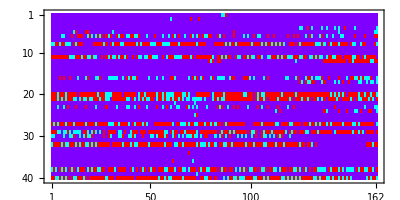

```mathematica
hsBOS07//(#/.{True->1,False->0,"DNP"->0.5})&//MatrixPlot[#,AspectRatio->1/2,ColorFunction->Hue]&
```

A small change (see yellow)  in the definion on LongestStreak (assumed Hitting) will determine the longest hitless streak:

```mathematica
LongestHitlessStreak[player_,gamelist_]:=HitSafelyQ[player,#]&/@gamelist//Select[#,#=!="DNP"&]&//Split[#]&//Map[{First[#],Length[#]}&,#]&//Select[#,Not[First[#]]&]&//If[#=={},0,Sort[#]//Last//Last]&
```

Julio Lugo had a particularly bad slump in 2007.

```mathematica
{FromPlayerCode[#],LongestHitlessStreak[#,temp]}&/@(Roster["BOS",2007]//Transpose//First)
```

(Jeff Bailey | 2
Josh Beckett | 1
Clay Buchholz | 0
Kevin Cash | 5
Royce Clayton | 3
Alex Cora | 4
Bryan Corey | 0
Coco Crisp | 4
Manny Delcarmen | 0
Brendan Donnelly | 0
J.D. Drew | 4
Jacoby Ellsbury | 2
Kason Gabbard | 0
Eric Gagne | 0
Devern Hansack | 0
Eric Hinske | 6
Bobby Kielty | 6
Jon Lester | 0
Javier Lopez | 0
Mike Lowell | 4
Julio Lugo | 10
Daisuke Matsuzaka | 2
Doug Mirabelli | 4
Brandon Moss | 2
David Murphy | 1
Hideki Okajima | 0
David Ortiz | 3
Jonathan Papelbon | 0
Dustin Pedroia | 5
Wily Mo Pena | 5
Joel Pineiro | 0
Manny Ramirez | 3
J.C. Romero | 0
Curt Schilling | 0
Kyle Snyder | 0
Julian Tavarez | 1
Mike Timlin | 0
Jason Varitek | 5
Tim Wakefield | 1
Kevin Youkilis | 3)

## Scorecard format

This idea hasn't been developed, but generating a scorecard format of a retrogame would be interesting.

```mathematica
t=AllEvents["SDN",1991]//First
```

SFN @ SDN on 1991/04/09

```mathematica
s1=InningsWithPitchers[t]//Partition[Append[#,{}],2]&//Transpose//First
```

{(SDN199104090 | play(1,0,thomr003,12,CBCFX,3/G34) | white001
SDN199104090 | play(1,0,mcgew001,1,CX,63/G6M) | white001
SDN199104090 | play(1,0,clarw001,0,X,3/G3) | white001),(SDN199104090 | play(2,0,mitck001,12,FFBS,K) | white001
SDN199104090 | play(2,0,willm003,0,X,13/G15S) | white001
SDN199104090 | play(2,0,bassk001,12,CBFFS,K) | white001),(SDN199104090 | play(3,0,decks001,30,BBBB,W) | white001
SDN199104090 | play(3,0,benjm001,11,CBX,8/L8RXD) | white001
SDN199104090 | play(3,0,burkj001,1,1LX,54/SH/B25.1-2) | white001
SDN199104090 | play(3,0,thomr003,32,CBFFFBFFBX,8/F78M) | white001),(SDN199104090 | play(4,0,mcgew001,2,FFFX,13/G34S) | white001
SDN199104090 | play(4,0,clarw001,2,FFX,E3/G3L.B-1) | white001
SDN199104090 | play(4,0,mitck001,0,X,HR/L78XD.1-H(UR)) | white001
SDN199104090 | play(4,0,willm003,11,BSX,9/F8RM) | white001
SDN199104090 | play(4,0,bassk001,21,CBBX,13/G15) | white001),(SDN199104090 | play(5,0,decks001,11,CBX,9/F8RS) | white001
SDN199104090 | play(5,0,benjm001,10,BX,6/P6MD) | white001
SDN199104090 | play(5,0,burkj001,2,CFC,K) | white001),(SDN199104090 | play(6,0,thomr003,10,BX,43/G4M) | white001
SDN199104090 | play(6,0,mcgew001,11,CBX,S6/G6) | white001
SDN199104090 | play(6,0,clarw001,32,1CB11BB>F>X,13/G15S.1-2) | white001
SDN199104090 | play(6,0,mitck001,20,BBX,63/G56) | white001),(SDN199104090 | play(7,0,willm003,22,SBBSX,63/G6M) | white001
SDN199104090 | play(7,0,bassk001,11,CBX,31/G34S) | white001
SDN199104090 | play(7,0,decks001,22,BCBCFX,E5/TH/G5.B-1) | white001
SDN199104090 | play(7,0,benjm001,1,CX,7/F7S) | white001),(SDN199104090 | play(8,0,burkj001,0,,NP) | white001
SDN199104090 | sub(feldm001,Mike Felder,0,9,11) | np
SDN199104090 | play(8,0,feldm001,2,.CLX,3/G3) | white001
SDN199104090 | play(8,0,thomr003,32,FBCFBFBB,W) | white001
SDN199104090 | play(8,0,mcgew001,0,X,S/BG56S.1-2) | white001
SDN199104090 | play(8,0,clarw001,0,,NP) | white001
SDN199104090 | sub(leffc001,Craig Lefferts,1,9,1) | np
SDN199104090 | play(8,0,clarw001,32,..BBCBSX,T8/L8LXD.2-H;1-H) | leffc001
SDN199104090 | play(8,0,mitck001,22,BBFSX,5/L56S) | leffc001
SDN199104090 | play(8,0,willm003,0,,NP) | leffc001
SDN199104090 | sub(maddm002,Mike Maddux,1,9,1) | np
SDN199104090 | play(8,0,willm003,12,..FFBX,63/G6M) | maddm002),(SDN199104090 | play(9,0,bassk001,0,,NP) | maddm002
SDN199104090 | sub(andel001,Larry Andersen,1,9,1) | np
SDN199104090 | play(9,0,bassk001,0,,NP) | andel001
SDN199104090 | sub(farip001,Paul Faries,1,7,5) | np
SDN199104090 | play(9,0,bassk001,21,...BBCX,13/G13S) | andel001
SDN199104090 | play(9,0,decks001,30,BBBB,W) | andel001
SDN199104090 | play(9,0,benjm001,0,,NP) | andel001
SDN199104090 | sub(kingm001,Mike Kingery,0,8,11) | np
SDN199104090 | play(9,0,kingm001,21,.CBBX,C/E2.1-2;B-1) | andel001
SDN199104090 | play(9,0,branj001,0,,NP) | andel001
SDN199104090 | sub(leonm001,Mark Leonard,0,9,11) | np
SDN199104090 | play(9,0,leonm001,22,.BSSFBFFX,46(1)3/GDP/G4) | andel001)}

Some ideas in a disabled cell:

```mathematica
place=0;
Fold[Append[#1,PadLeft[#2,place+Length[#2],{"x"}]//(place=Mod[#,9];#)&//PadRight[#,9 Ceiling[Length[#]/9],{"x"}]&//peek]&,{},s1]
```

## PostSeason

```mathematica
WorldSeriesYears[]
```

{1903,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022}

```mathematica
series=WorldSeries[2004]
```

{SLN @ BOS on 2004/10/23,SLN @ BOS on 2004/10/24,BOS @ SLN on 2004/10/26,BOS @ SLN on 2004/10/27}

```mathematica
StartingBattingOrder[series[[1]],1]
```

(damoj001 | Johnny Damon
cabro001 | Orlando Cabrera
ramim002 | Manny Ramirez
ortid001 | David Ortiz
millk005 | Kevin Millar
nixot001 | Trot Nixon
muelb001 | Bill Mueller
mirad001 | Doug Mirabelli
bellm002 | Mark Bellhorn)

```mathematica
series[[1]]//HomePlateUmpire
```

{monte901,Ed Montague}

```mathematica
PostSeasonEvents[1969]
```

{1969ALCS.EVE,1969NLCS.EVE,1969WS.EVE}

```mathematica
LoadGames[PostSeasonEvents[1969][[1]]]
```

{MIN @ BAL on 1969/10/04,MIN @ BAL on 1969/10/05,BAL @ MIN on 1969/10/06}

```mathematica
ALCS[1986]
```

{CAL @ BOS on 1986/10/07,CAL @ BOS on 1986/10/08,BOS @ CAL on 1986/10/10,BOS @ CAL on 1986/10/11,BOS @ CAL on 1986/10/12,CAL @ BOS on 1986/10/14,CAL @ BOS on 1986/10/15}

```mathematica
NLDS[2000]
```

{{ATL @ SLN on 2000/10/03,ATL @ SLN on 2000/10/05,SLN @ ATL on 2000/10/07},{NYN @ SFN on 2000/10/04,NYN @ SFN on 2000/10/05,SFN @ NYN on 2000/10/07,SFN @ NYN on 2000/10/08}}

```mathematica
WildCardFiles[]
```

{}

```mathematica
WildCard["AL",2021]
```

WildCard::None: No wildcard games in 2021.

{}

## Position Graphs

```mathematica
Starter::usage="Starter[retrogame,teamcode,positionumber] returns a list with player code followed by name of player who started game for team at the indicated defensive position (1-9).";
```

```mathematica
StarterHistory::usage="StarterHistory[teamcode,positionnumber,{year0,year1}] returns a tally of the number of times each player on team started at position for each of the years year0 to year1";
```

```mathematica
Starter[game_,team_,position_]:=Module[{possibles},possibles=Cases[game,start[code_,name_,vh_,bo_,position]];If[VisitingTeam[game]==team,List@@possibles[[1,{1,2}]],List@@possibles[[2,{1,2}]]]]
```

```mathematica
g=First[AllEvents["BOS",1956]]
Starter[g,"BOS",7]
```

BAL @ BOS on 1956/04/17

{willt103,Ted Williams}

```mathematica
StarterHistory[team_,pos_,{year0_,year1_}]:=Table[Map[{y,Starter[#,team,pos]}&,AllEvents[team,y]]//Tally,{y,year0,year1}]//Map[Flatten/@#&,#]&
```

```mathematica
Teams[1919]
```

(NYA | NYA | AL |  | New York | Yankees |  | 1/1/1913 | 9/29/1968 | New York | NY
LAN | BRO | NL |  | Brooklyn | Robins |  | 1/1/1914 | 9/27/1931 | Brooklyn | NY
CLE | CLE | AL |  | Cleveland | Indians |  | 1/1/1915 | 9/27/1968 | Cleveland | OH
ATL | BSN | NL |  | Boston | Braves |  | 4/11/1912 | 9/29/1935 | Boston | MA
BOS | BOS | AL |  | Boston | Red Sox |  | 4/14/1908 | 9/29/1968 | Boston | MA
CHN | CHN | NL |  | Chicago | Cubs |  | 4/16/1903 | 9/29/1968 | Chicago | IL
CIN | CIN | NL |  | Cincinnati | Reds |  | 4/19/1890 | 9/27/1953 | Cincinnati | OH
PHI | PHI | NL |  | Philadelphia | Phillies |  | 4/19/1890 | 9/27/1942 | Philadelphia | PA
SLN | SLN | NL |  | St. Louis | Cardinals |  | 4/19/1900 | 9/29/1968 | St. Louis | MO
PIT | PIT | NL |  | Pittsburgh | Pirates |  | 4/22/1891 | 9/29/1968 | Pittsburgh | PA
BAL | SLA | AL |  | St. Louis | Browns |  | 4/23/1902 | 9/27/1953 | St. Louis | MO
CHA | CHA | AL |  | Chicago | White Sox |  | 4/24/1901 | 9/29/1968 | Chicago | IL
DET | DET | AL |  | Detroit | Tigers |  | 4/25/1901 | 9/29/1968 | Detroit | MI
MIN | WS1 | AL |  | Washington | Senators | Nationals | 4/26/1901 | 10/2/1960 | Washington | DC
OAK | PHA | AL |  | Philadelphia | Athletics | A's | 4/26/1901 | 9/26/1954 | Philadelphia | PA
SFN | NY1 | NL |  | New York | Giants |  | 5/2/1885 | 9/29/1957 | New York | NY)

t = #; StarterHistory[#, 1, {1960, 1969}] // {Min[Length /@ #] &

7

```mathematica
StarterHistory["SLN",1,{2000,2009}]
```

{(2000 | kiled001 | Darryl Kile | 34
2000 | hentp001 | Pat Hentgen | 33
2000 | stepg001 | Garrett Stephenson | 31
2000 | benea001 | Andy Benes | 27
2000 | ankir001 | Rick Ankiel | 30
2000 | reamb001 | Britt Reames | 7),(2001 | kiled001 | Darryl Kile | 34
2001 | benea001 | Andy Benes | 19
2001 | morrm001 | Matt Morris | 34
2001 | hermd001 | Dustin Hermanson | 33
2001 | ankir001 | Rick Ankiel | 6
2001 | mattm001 | Mike Matthews | 10
2001 | smitb004 | Bud Smith | 14
2001 | willw001 | Woody Williams | 11
2001 | benea002 | Alan Benes | 1),(2002 | morrm001 | Matt Morris | 32
2002 | stepg001 | Garrett Stephenson | 10
2002 | benea001 | Andy Benes | 17
2002 | willw001 | Woody Williams | 17
2002 | kiled001 | Darryl Kile | 14
2002 | smitb004 | Bud Smith | 10
2002 | timlm001 | Mike Timlin | 1
2002 | pearj001 | Josh Pearce | 3
2002 | smitt001 | Travis Smith | 10
2002 | crudm001 | Mike Crudale | 1
2002 | simoj001 | Jason Simontacchi | 24
2002 | hackl001 | Luther Hackman | 6
2002 | finlc001 | Chuck Finley | 14
2002 | wrigj001 | Jamey Wright | 3),(2003 | morrm001 | Matt Morris | 27
2003 | willw001 | Woody Williams | 33
2003 | stepg001 | Garrett Stephenson | 27
2003 | tomkb001 | Brett Tomko | 32
2003 | simoj001 | Jason Simontacchi | 16
2003 | calek001 | Kiko Calero | 1
2003 | hared001 | Danny Haren | 1
2003 | hared001 | Dan Haren | 13
2003 | fassj001 | Jeff Fassero | 6
2003 | hitcs001 | Sterling Hitchcock | 6),(2004 | morrm001 | Matt Morris | 32
2004 | marqj001 | Jason Marquis | 32
2004 | willw001 | Woody Williams | 31
2004 | suppj001 | Jeff Suppan | 31
2004 | carpc002 | Chris Carpenter | 28
2004 | hared001 | Dan Haren | 5
2004 | reyea001 | Al Reyes | 2
2004 | florr001 | Randy Flores | 1),(2005 | carpc002 | Chris Carpenter | 33
2005 | marqj001 | Jason Marquis | 32
2005 | muldm001 | Mark Mulder | 32
2005 | suppj001 | Jeff Suppan | 32
2005 | morrm001 | Matt Morris | 31
2005 | reyea002 | Anthony Reyes | 1
2005 | eldrc001 | Cal Eldred | 1),(2006 | carpc002 | Chris Carpenter | 32
2006 | muldm001 | Mark Mulder | 17
2006 | marqj001 | Jason Marquis | 33
2006 | suppj001 | Jeff Suppan | 32
2006 | ponss001 | Sidney Ponson | 13
2006 | reyea002 | Anthony Reyes | 17
2006 | thomb002 | Brad Thompson | 1
2006 | weavj002 | Jeff Weaver | 15
2006 | narvc001 | Chris Narveson | 1),(2007 | carpc002 | Chris Carpenter | 1
2007 | wellk001 | Kip Wells | 26
2007 | loopb001 | Braden Looper | 30
2007 | waina001 | Adam Wainwright | 32
2007 | reyea002 | Anthony Reyes | 20
2007 | keisr001 | Randy Keisler | 3
2007 | thomb002 | Brad Thompson | 17
2007 | wellt002 | Todd Wellemeyer | 11
2007 | marom001 | Mike Maroth | 7
2007 | pinej001 | Joel Pineiro | 11
2007 | muldm001 | Mark Mulder | 3
2007 | perct001 | Troy Percival | 1),(2008 | lohsk001 | Kyle Lohse | 33
2008 | wellt002 | Todd Wellemeyer | 32
2008 | thomb002 | Brad Thompson | 6
2008 | loopb001 | Braden Looper | 33
2008 | waina001 | Adam Wainwright | 20
2008 | pinej001 | Joel Pineiro | 25
2008 | parim001 | Mike Parisi | 2
2008 | boggm001 | Mitchell Boggs | 6
2008 | muldm001 | Mark Mulder | 1
2008 | garcj004 | Jaime Garcia | 1
2008 | carpc002 | Chris Carpenter | 3),(2009 | waina001 | Adam Wainwright | 34
2009 | lohsk001 | Kyle Lohse | 22
2009 | wellt002 | Todd Wellemeyer | 21
2009 | carpc002 | Chris Carpenter | 28
2009 | pinej001 | Joel Pineiro | 32
2009 | waltp001 | P.J. Walters | 1
2009 | boggm001 | Mitchell Boggs | 9
2009 | thomb002 | Brad Thompson | 8
2009 | smolj001 | John Smoltz | 7)}

```mathematica
StarterHistory["LAN", 1, {1960, 1969}]
```

{(1960 | drysd101 | Don Drysdale | 36
1960 | sherl101 | Larry Sherry | 3
1960 | podrj101 | Johnny Podres | 33
1960 | koufs101 | Sandy Koufax | 26
1960 | mcded101 | Danny McDevitt | 7
1960 | crair101 | Roger Craig | 15
1960 | wills102 | Stan Williams | 30
1960 | rakoe101 | Ed Rakow | 2
1960 | goldj102 | Jim Golden | 1
1960 | ortep101 | Phil Ortega | 1),(1961 | drysd101 | Don Drysdale | 37
1961 | podrj101 | Johnny Podres | 29
1961 | crair101 | Roger Craig | 14
1961 | koufs101 | Sandy Koufax | 35
1961 | wills102 | Stan Williams | 35
1961 | perrr101 | Ron Perranoski | 1
1961 | sherl101 | Larry Sherry | 1
1961 | ortep101 | Phil Ortega | 2),(1962 | podrj101 | Johnny Podres | 40
1962 | koufs101 | Sandy Koufax | 26
1962 | wills102 | Stan Williams | 28
1962 | drysd101 | Don Drysdale | 41
1962 | moelj101 | Joe Moeller | 15
1962 | richp102 | Pete Richert | 12
1962 | ortep101 | Phil Ortega | 3),(1963 | drysd101 | Don Drysdale | 42
1963 | koufs101 | Sandy Koufax | 40
1963 | podrj101 | Johnny Podres | 34
1963 | millb106 | Bob Miller | 23
1963 | richp102 | Pete Richert | 12
1963 | sherl101 | Larry Sherry | 3
1963 | willn101 | Nick Willhite | 8
1963 | calmd101 | Dick Calmus | 1),(1964 | koufs101 | Sandy Koufax | 28
1964 | drysd101 | Don Drysdale | 40
1964 | millb106 | Bob Miller | 2
1964 | richp102 | Pete Richert | 6
1964 | willn101 | Nick Willhite | 7
1964 | moelj101 | Joe Moeller | 24
1964 | podrj101 | Johnny Podres | 2
1964 | ortep101 | Phil Ortega | 25
1964 | reedh102 | Howie Reed | 7
1964 | milll101 | Larry Miller | 14
1964 | brewj102 | Jim Brewer | 5
1964 | singb101 | Bill Singer | 2
1964 | purdj101 | John Purdin | 2),(1965 | drysd101 | Don Drysdale | 42
1965 | ostec103 | Claude Osteen | 40
1965 | koufs101 | Sandy Koufax | 41
1965 | podrj101 | Johnny Podres | 22
1965 | purdj101 | John Purdin | 2
1965 | brewj102 | Jim Brewer | 2
1965 | reedh102 | Howie Reed | 5
1965 | kekim101 | Mike Kekich | 1
1965 | willn101 | Nick Willhite | 6
1965 | millb106 | Bob Miller | 1),(1966 | ostec103 | Claude Osteen | 38
1966 | koufs101 | Sandy Koufax | 41
1966 | suttd001 | Don Sutton | 35
1966 | drysd101 | Don Drysdale | 40
1966 | moelj101 | Joe Moeller | 8),(1967 | millb106 | Bob Miller | 4
1967 | ostec103 | Claude Osteen | 39
1967 | suttd001 | Don Sutton | 34
1967 | drysd101 | Don Drysdale | 38
1967 | brewj102 | Jim Brewer | 11
1967 | singb101 | Bill Singer | 29
1967 | regap101 | Phil Regan | 3
1967 | duffj101 | John Duffie | 2
1967 | fosta101 | Alan Foster | 2),(1968 | ostec103 | Claude Osteen | 36
1968 | singb101 | Bill Singer | 36
1968 | drysd101 | Don Drysdale | 29
1968 | kekim101 | Mike Kekich | 19
1968 | granj101 | Jim Grant | 4
1968 | suttd001 | Don Sutton | 27
1968 | billj101 | Jack Billingham | 1
1968 | purdj101 | John Purdin | 1
1968 | moelj101 | Joe Moeller | 3
1968 | fosta101 | Alan Foster | 3),(1969 | drysd101 | Don Drysdale | 12
1969 | suttd001 | Don Sutton | 41
1969 | ostec103 | Claude Osteen | 41
1969 | singb101 | Bill Singer | 40
1969 | fosta101 | Alan Foster | 15
1969 | moelj101 | Joe Moeller | 4
1969 | bunnj101 | Jim Bunning | 9)}

```mathematica
StarterHistory["NYA",1,{1950,1964}]
```

{(1950 | reyna102 | Allie Reynolds | 25
1950 | lopae101 | Eddie Lopat | 28
1950 | byrnt101 | Tommy Byrne | 29
1950 | portb102 | Bob Porterfield | 2
1950 | sanff101 | Fred Sanford | 9
1950 | rascv101 | Vic Raschi | 27
1950 | ostrj101 | Joe Ostrowski | 4
1950 | fordw101 | Whitey Ford | 10
1950 | nevee102 | Ernie Nevel | 1),(1951 | rascv101 | Vic Raschi | 32
1951 | lopae101 | Eddie Lopat | 30
1951 | morgt101 | Tom Morgan | 14
1951 | byrnt101 | Tommy Byrne | 3
1951 | sheas101 | Spec Shea | 11
1951 | reyna102 | Allie Reynolds | 25
1951 | ostrj101 | Joe Ostrowski | 2
1951 | sanff101 | Fred Sanford | 2
1951 | kramj101 | Jack Kramer | 3
1951 | overs101 | Stubby Overmire | 4
1951 | kuzab101 | Bob Kuzava | 7
1951 | schaa102 | Art Schallock | 3
1951 | wiesb101 | Bob Wiesler | 3
1951 | sainj101 | Johnny Sain | 4),(1952 | rascv101 | Vic Raschi | 29
1952 | lopae101 | Eddie Lopat | 17
1952 | reyna102 | Allie Reynolds | 22
1952 | morgt101 | Tom Morgan | 12
1952 | millb104 | Bill Miller | 11
1952 | sainj101 | Johnny Sain | 14
1952 | lopae101 | Ed Lopat | 2
1952 | mcdoj104 | Jim McDonald | 5
1952 | kuzab101 | Bob Kuzava | 11
1952 | ostrj101 | Joe Ostrowski | 1
1952 | gormt102 | Tom Gorman | 6
1952 | schah102 | Harry Schaeffer | 2
1952 | schmj101 | Johnny Schmitz | 2
1952 | scarr102 | Ray Scarborough | 4
1952 | blace102 | Ewell Blackwell | 2),(1953 | rascv101 | Vic Raschi | 25
1953 | reyna102 | Allie Reynolds | 15
1953 | sainj101 | Johnny Sain | 16
1953 | lopae101 | Eddie Lopat | 22
1953 | mcdoj104 | Jim McDonald | 18
1953 | blace102 | Ewell Blackwell | 4
1953 | fordw101 | Whitey Ford | 29
1953 | scarr102 | Ray Scarborough | 1
1953 | kuzab101 | Bob Kuzava | 5
1953 | gormt102 | Tom Gorman | 1
1953 | millb104 | Bill Miller | 3
1953 | krals101 | Steve Kraly | 3
1953 | lopae101 | Ed Lopat | 1),(1954 | fordw101 | Whitey Ford | 28
1954 | lopae101 | Eddie Lopat | 23
1954 | morgt101 | Tom Morgan | 16
1954 | grimb102 | Bob Grim | 20
1954 | mcdoj104 | Jim McDonald | 10
1954 | byrdh101 | Harry Byrd | 21
1954 | millb104 | Bill Miller | 1
1954 | reyna102 | Allie Reynolds | 17
1954 | kuzab101 | Bob Kuzava | 3
1954 | wiesb101 | Bob Wiesler | 5
1954 | branr103 | Ralph Branca | 3
1954 | byrnt101 | Tommy Byrne | 5
1954 | schaa102 | Art Schallock | 1),(1955 | fordw101 | Whitey Ford | 33
1955 | grimb102 | Bob Grim | 11
1955 | turlb101 | Bob Turley | 34
1955 | byrnt101 | Tommy Byrne | 22
1955 | lopae101 | Eddie Lopat | 12
1955 | kuckj101 | Johnny Kucks | 13
1955 | wiesb101 | Bob Wiesler | 7
1955 | larsd102 | Don Larsen | 13
1955 | morgt101 | Tom Morgan | 1
1955 | grayt101 | Ted Gray | 1
1955 | sturt101 | Tom Sturdivant | 1
1955 | coler101 | Rip Coleman | 6),(1956 | larsd102 | Don Larsen | 20
1956 | kuckj101 | Johnny Kucks | 31
1956 | mcdem102 | Mickey McDermott | 9
1956 | fordw101 | Whitey Ford | 30
1956 | turlb101 | Bob Turley | 21
1956 | byrnt101 | Tommy Byrne | 8
1956 | coler101 | Rip Coleman | 9
1956 | sturt101 | Tom Sturdivant | 17
1956 | grimb102 | Bob Grim | 6
1956 | terrr101 | Ralph Terry | 3),(1957 | fordw101 | Whitey Ford | 17
1957 | kuckj101 | Johnny Kucks | 23
1957 | larsd102 | Don Larsen | 20
1957 | sturt101 | Tom Sturdivant | 28
1957 | ditma101 | Art Ditmar | 11
1957 | shanb102 | Bobby Shantz | 21
1957 | turlb101 | Bob Turley | 23
1957 | cicoa101 | Al Cicotte | 2
1957 | terrr101 | Ralph Terry | 2
1957 | byrnt101 | Tommy Byrne | 4
1957 | magls101 | Sal Maglie | 3),(1958 | larsd102 | Don Larsen | 19
1958 | sturt101 | Tom Sturdivant | 10
1958 | kuckj101 | Johnny Kucks | 15
1958 | fordw101 | Whitey Ford | 29
1958 | shanb102 | Bobby Shantz | 13
1958 | turlb101 | Bob Turley | 31
1958 | magls101 | Sal Maglie | 3
1958 | ditma101 | Art Ditmar | 13
1958 | maasd101 | Duke Maas | 13
1958 | monrz101 | Zach Monroe | 6
1958 | dickm101 | Murry Dickson | 2
1958 | durer101 | Ryne Duren | 1),(1959 | turlb101 | Bob Turley | 22
1959 | larsd102 | Don Larsen | 18
1959 | fordw101 | Whitey Ford | 29
1959 | ditma101 | Art Ditmar | 25
1959 | maasd101 | Duke Maas | 21
1959 | kuckj101 | Johnny Kucks | 1
1959 | sturt101 | Tom Sturdivant | 3
1959 | shanb102 | Bobby Shantz | 4
1959 | terrr101 | Ralph Terry | 16
1959 | bronj101 | Jim Bronstad | 3
1959 | grbae101 | Eli Grba | 6
1959 | blayg101 | Gary Blaylock | 1
1959 | coatj101 | Jim Coates | 4
1959 | freem101 | Mark Freeman | 1
1959 | gablg102 | Gabe Gabler | 1),(1960 | coatj101 | Jim Coates | 18
1960 | turlb101 | Bob Turley | 24
1960 | gablg102 | Gabe Gabler | 4
1960 | fordw101 | Whitey Ford | 29
1960 | shorb101 | Bill Short | 10
1960 | terrr101 | Ralph Terry | 23
1960 | ditma101 | Art Ditmar | 28
1960 | maasd101 | Duke Maas | 1
1960 | grbae101 | Eli Grba | 9
1960 | stafb101 | Bill Stafford | 8
1960 | durer101 | Ryne Duren | 1),(1961 | fordw101 | Whitey Ford | 39
1961 | turlb101 | Bob Turley | 12
1961 | ditma101 | Art Ditmar | 8
1961 | coatj101 | Jim Coates | 11
1961 | terrr101 | Ralph Terry | 27
1961 | mcded101 | Danny McDevitt | 2
1961 | shelr101 | Rollie Sheldon | 21
1961 | stafb101 | Bill Stafford | 25
1961 | daleb102 | Bud Daley | 17
1961 | downa101 | Al Downing | 1),(1962 | fordw101 | Whitey Ford | 37
1962 | stafb101 | Bill Stafford | 33
1962 | terrr101 | Ralph Terry | 39
1962 | coatj101 | Jim Coates | 6
1962 | daleb102 | Bud Daley | 6
1962 | shelr101 | Rollie Sheldon | 16
1962 | boutj101 | Jim Bouton | 16
1962 | turlb101 | Bob Turley | 8
1962 | browh101 | Hal Brown | 1),(1963 | terrr101 | Ralph Terry | 37
1963 | stafb101 | Bill Stafford | 14
1963 | fordw101 | Whitey Ford | 37
1963 | wills102 | Stan Williams | 21
1963 | boutj101 | Jim Bouton | 30
1963 | downa101 | Al Downing | 22),(1964 | fordw101 | Whitey Ford | 36
1964 | boutj101 | Jim Bouton | 37
1964 | downa101 | Al Downing | 35
1964 | daleb102 | Bud Daley | 3
1964 | meyeb102 | Bob Meyer | 1
1964 | terrr101 | Ralph Terry | 14
1964 | wills102 | Stan Williams | 10
1964 | stafb101 | Bill Stafford | 1
1964 | hamis101 | Steve Hamilton | 3
1964 | shelr101 | Rollie Sheldon | 12
1964 | stotm101 | Mel Stottlemyre | 12)}

```mathematica
PositionRuns[team_,pos_,{year0_,year1_},cutoff_:4]:=StarterHistory[team,pos,{year0,year1}]//Flatten[#,1]&//SortBy[#,#[[2]]&]&//SplitBy[#,#[[2]]&]&//Select[#,Length[#]>=cutoff&]&//Map[Flatten/@#&,#]&
```

```mathematica
PositionRuns["NYA",2,{1950,1962}]
```

{(1950 | berry101 | Yogi Berra | 128
1951 | berry101 | Yogi Berra | 129
1952 | berry101 | Yogi Berra | 125
1953 | berry101 | Yogi Berra | 118
1954 | berry101 | Yogi Berra | 146
1955 | berry101 | Yogi Berra | 141
1956 | berry101 | Yogi Berra | 134
1957 | berry101 | Yogi Berra | 116
1958 | berry101 | Yogi Berra | 87
1959 | berry101 | Yogi Berra | 112
1960 | berry101 | Yogi Berra | 53
1961 | berry101 | Yogi Berra | 15
1962 | berry101 | Yogi Berra | 28),(1955 | blanj101 | Johnny Blanchard | 1
1959 | blanj101 | Johnny Blanchard | 2
1960 | blanj101 | Johnny Blanchard | 21
1961 | blanj101 | Johnny Blanchard | 42
1962 | blanj101 | Johnny Blanchard | 10),(1955 | howae101 | Elston Howard | 4
1956 | howae101 | Elston Howard | 19
1957 | howae101 | Elston Howard | 26
1958 | howae101 | Elston Howard | 64
1959 | howae101 | Elston Howard | 41
1960 | howae101 | Elston Howard | 80
1961 | howae101 | Elston Howard | 106
1962 | howae101 | Elston Howard | 124),(1950 | silvc101 | Charlie Silvera | 6
1951 | silvc101 | Charlie Silvera | 12
1952 | silvc101 | Charlie Silvera | 15
1953 | silvc101 | Charlie Silvera | 23
1954 | silvc101 | Charlie Silvera | 6
1955 | silvc101 | Charlie Silvera | 7
1956 | silvc101 | Charlie Silvera | 1)}

```mathematica
playerRunGraph[playerRun_,{year0_,year1_}]:={Map[Text[Tooltip[ToString[#[[1]]]<>"\n"<>(#[[3]]//StringSplit//Last)<>"\n"<>ToString[#[[4]]]],{#[[1]],#[[4]]}]&,playerRun],RandomColor[],Line[playerRun[[All,{1,4}]]]}//Graphics[#,PlotRange->{{year0-5,year1+5},{-20,170}}]&
```

```mathematica
PositionHistoryGraph[team_,pos_,{year0_,year1_},cutoff_:4]:=Map[playerRunGraph,PositionRuns[team,pos,{year0,year1},cutoff]]//Show[#,AspectRatio->1/2,ImageSize->1500]&
```

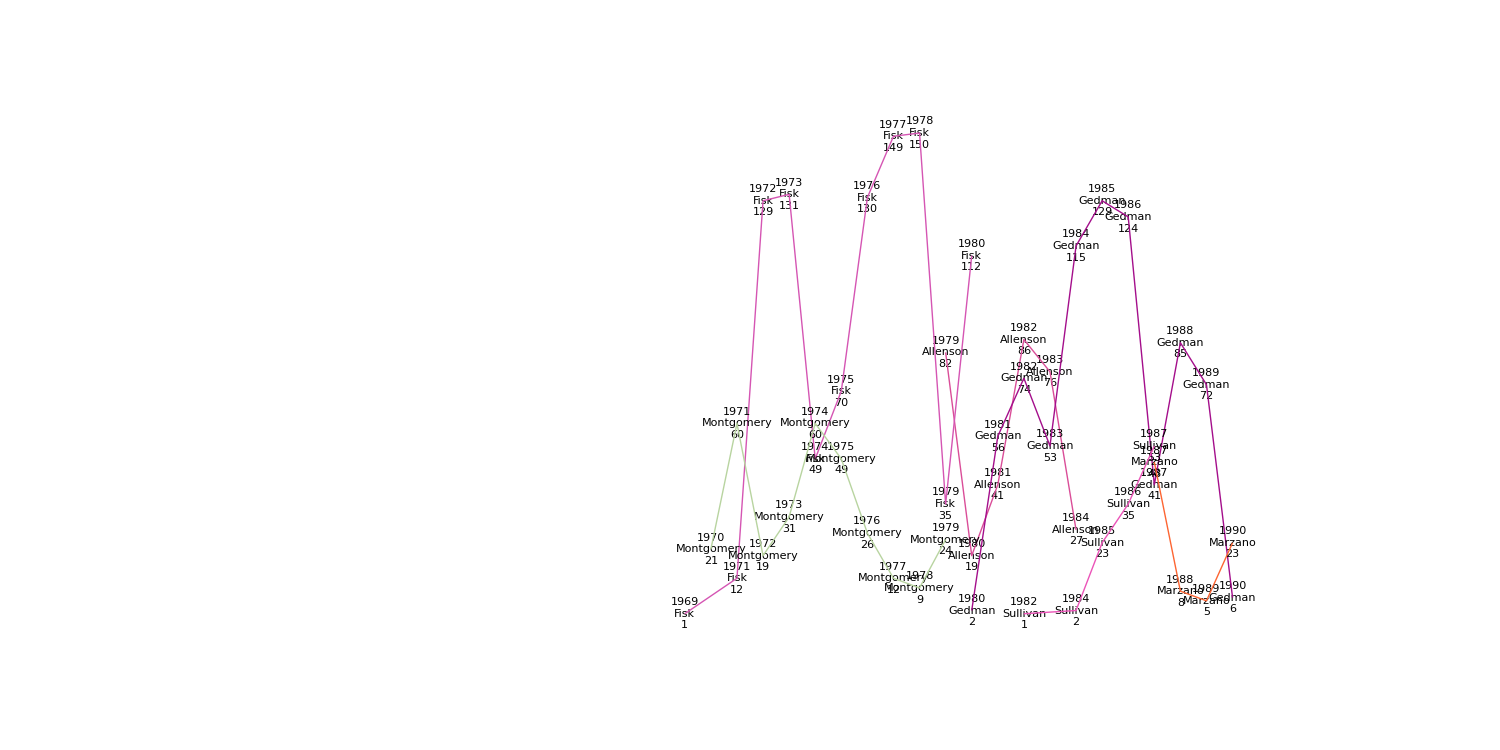

```mathematica
PositionHistoryGraph["BOS",2,{1969,1990},4]
```

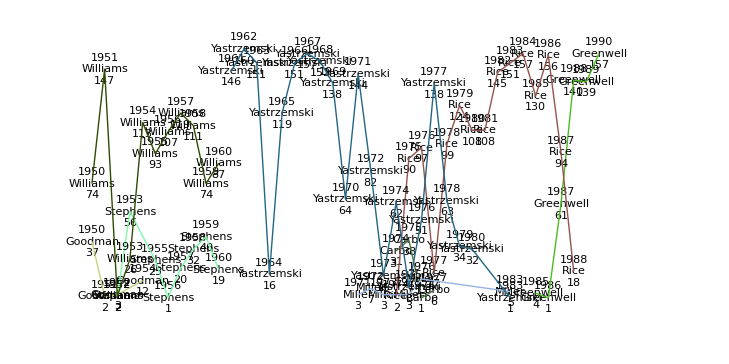

```mathematica
Map[playerRunGraph,prs]//Show[#,AspectRatio->1/2]&
```

```mathematica
ex=Flatten[history,1]//SortBy[#,#[[1,2,1]]&]&//SplitBy[#,#[[1,2,1]]&]&//Select[#,Length[#]>=4&]&//First
```

({1974,{carbb101,Bernie Carbo}} | 31
{1975,{carbb101,Bernie Carbo}} | 38
{1976,{carbb101,Bernie Carbo}} | 1
{1977,{carbb101,Bernie Carbo}} | 6)

```mathematica
yearlyplot=ListPlot[Map[Tooltip[{#[[1,1]],Last[#]},#[[1,2,2]]]&,#],Joined->True]&
```

ListPlot[({#1⟦1,1⟧,Last[#1]}&)/@#1,Joined→True]&

```mathematica
SequenceCases[GameLogData[game][[Range[106,159]]],{code_,name_,6}]
```

(petrr101 | Rico Petrocelli | 6
brine101 | Ed Brinkman | 6)

```mathematica
Starters[year_,team_,position_]:=Module[{season},season=AllEvents[team,year];
StartingBattingOrder[]]
```